```mathematica
PlanckRadiationLaw[]
```

PlanckRadiationLaw::argrx: PlanckRadiationLaw called with 0 arguments; 2 arguments are expected.

PlanckRadiationLaw[]

```mathematica
TrigToExp[RotationMatrix[180 Degree]]//MatrixForm
```

(-1 | 0
0 | -1)

```mathematica
TrigToExp[RotationMatrix[90 Degree]]//MatrixForm
```

```mathematica
Solve[x^2-x-1  == 0,x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
Solve[x^4-(x^2-x-1)^2  == 0,x]
```

{{x→-1},{x→-1/2},{x→1}}

```mathematica
Solve[x^8(-x^4-(x^2-x-1)^2)^2  == 0,x]
```

{{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→Root-0.556-0.138 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,1]-0.5563468638492699},{x→Root-0.556-0.138 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,1]-0.5563468638492699},{x→Root-0.556+0.138 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,2]-0.5563468638492699},{x→Root-0.556+0.138 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,2]-0.5563468638492699},{x→Root1.06-0.638 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,3]1.05634686384927},{x→Root1.06-0.638 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,3]1.05634686384927},{x→Root1.06+0.638 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,4]1.05634686384927},{x→Root1.06+0.638 ⅈRoot[1+2 #1-#1^2-2 #1^3+2 #1^4&,4]1.05634686384927}}

```mathematica
√5//N
```

2.23607

## The Not Defines Orthonormality

#### Concept Orthonormality

#### Orthonormality

```mathematica
FullForm[Orthogonalize]
```

Orthogonalize

```mathematica
Factorial[0]
```

1

```mathematica
PickAnN=13
```

13

```mathematica
Clear[NotNull]
```

```mathematica
Clear[PickAnN]
```

```mathematica
(*NotNull= 1/PickAnN*)
```

1/13

```mathematica
Unity=Sum[NotNull[ThisNotNull],{ThisNotNull,0,Infinity}]
```

∑_(ThisNotNull=0)^∞ NotNull[ThisNotNull]

```mathematica
Integrate[NotNull[ThisNotNull],{ThisNotNull,0,Infinity}]
```

∫_0^∞ NotNull[ThisNotNull]ⅆThisNotNull

```mathematica
Limit[Integrate[NotNull[ThisNotNull],{ThisNotNull,0,Infinity}]]
```

```mathematica
∑_(ThisNotNull=0)^∞ (1/13)[ThisNotNull]//N
```

NSum::nsnum: Summand (or its derivative) 1/13[ThisNotNull] is not numerical at point ThisNotNull = 46661.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

NSum[1/13[ThisNotNull],{ThisNotNull,0,∞}]

```mathematica
Unity=Sum[NotNull[ThisNotNull],{ThisNotNull,-Infinity,Infinity}]
```

∑_(ThisNotNull=-∞)^∞ NotNull[ThisNotNull]

```mathematica
∑_(ThisNotNull=-∞)^∞ (1/13)[ThisNotNull]//N
```

NSum::nsnum: Summand (or its derivative) 1/13[ThisNotNull] is not numerical at point ThisNotNull = 46661.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

NSum[1/13[ThisNotNull],{ThisNotNull,-∞,∞}]

```mathematica
Unity=Sum[NotNull[ThisNotNull],{ThisNotNull,-PickAnN,PickAnN}]
```

```mathematica
∑_(ThisNotNull=-PickAnN)^PickAnN NotNull[ThisNotNull]
```

```mathematica
Unity=Simplify[Sum[NotNull[ThisNotNull],{ThisNotNull,-PickAnN-1,PickAnN+1}]]
```

```mathematica
∑_(ThisNotNull=-1-PickAnN)^(1+PickAnN) NotNull[ThisNotNull]
```

```mathematica
Unity=Sum[NotNull[ThisNotNull],{ThisNotNull,-PickAnN-1,PickAnN+1}]
```

```mathematica
∑_(ThisNotNull=-1-PickAnN)^(1+PickAnN) NotNull[ThisNotNull]
```

```mathematica
{0,-Unity}
{0,-Unity}//MatrixForm
{0,-Unity}//ReflectionMatrix
{0,-Unity}//ReflectionTransform
{0,-Unity}//Conjugate
```

{0,-Unity}

(0
-Unity)

{{1,0},{0,1-(2 Unity Conjugate[Unity])/Abs[Unity]^2}}

TransformationFunction[(1 | 0 | 0
0 | (Abs[Unity]^2-2 Unity Conjugate[Unity])/Abs[Unity]^2 | 0
0 | 0 | 1)]

{0,-Conjugate[Unity]}

```mathematica
{{0},-{Unity}}
{{0},-{Unity}}//MatrixForm
{{0},-{Unity}}//ReflectionMatrix
{{0},-{Unity}}//ReflectionTransform
{{0},-{Unity}}//Conjugate
```

{{0},{-Unity}}

(0
-Unity)

ReflectionMatrix::inpv: {{0},{-Unity}} is not a vector.

ReflectionMatrix[{{0},{-Unity}}]

ReflectionTransform::inpv: {{0},{-Unity}} is not a vector.

ReflectionTransform[{{0},{-Unity}}]

{{0},{-Conjugate[Unity]}}

```mathematica
Unity=I
```

ⅈ

```mathematica
{0,-Unity}
{0,-Unity}//MatrixForm
{0,-Unity}//ReflectionMatrix
{0,-Unity}//ReflectionTransform
{0,-Unity}//Conjugate
```

{0,-ⅈ}

(0
-ⅈ)

{{1,0},{0,-1}}

TransformationFunction[(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)]

{0,ⅈ}

```mathematica
Unity=-1
```

-1

```mathematica
{0,-Unity}
{0,-Unity}//MatrixForm
{0,-Unity}//ReflectionMatrix
{0,-Unity}//ReflectionTransform
{0,-Unity}//Conjugate
```

{0,1}

(0
1)

{{1,0},{0,-1}}

TransformationFunction[(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)]

{0,1}

```mathematica
¤
```

¤

```mathematica
{0,¤}
{0,¤}//MatrixForm
{0,¤}//ReflectionMatrix
{0,¤}//ReflectionTransform
{0,¤}//Conjugate
```

{0,¤}

(0
¤)

{{1,0},{0,1-(2 ¤ Conjugate[¤])/Abs[¤]^2}}

TransformationFunction[(1 | 0 | 0
0 | (Abs[¤]^2-2 ¤ Conjugate[¤])/Abs[¤]^2 | 0
0 | 0 | 1)]

{0,Conjugate[¤]}

```mathematica
¤=-1
```

-1

```mathematica
{0,¤}
{0,¤}//MatrixForm
{0,¤}//ReflectionMatrix
{0,¤}//ReflectionTransform
{0,¤}//Conjugate
```

```mathematica
Clear[¤]
{0,¤}
{0,¤}//MatrixForm
{0,¤}//ReflectionMatrix
{0,¤}//ReflectionTransform
{0,¤}//Conjugate
```

{0,¤}

(0
¤)

{{1,0},{0,1-(2 ¤ Conjugate[¤])/Abs[¤]^2}}

TransformationFunction[(1 | 0 | 0
0 | (Abs[¤]^2-2 ¤ Conjugate[¤])/Abs[¤]^2 | 0
0 | 0 | 1)]

{0,Conjugate[¤]}

```mathematica
FullForm[-I]
```

```mathematica
Quartics
```

Complex[0,-1]

```mathematica
¤Ver=-I
¤InVer=+I
¤ ={¤Ver,¤InVer}

{0,¤}
{0,¤}//MatrixForm
{0,¤}//ReflectionMatrix
{0,¤}//ReflectionTransform
{0,¤}//Conjugate
```

-ⅈ

ⅈ

{-ⅈ,ⅈ}

{0,{-ⅈ,ⅈ}}

(0
{-ⅈ,ⅈ})

ReflectionMatrix::inpv: {0,{-ⅈ,ⅈ}} is not a vector.

ReflectionMatrix[{0,{-ⅈ,ⅈ}}]

ReflectionTransform::inpv: {0,{-ⅈ,ⅈ}} is not a vector.

ReflectionTransform[{0,{-ⅈ,ⅈ}}]

{0,{ⅈ,-ⅈ}}

```mathematica
`
```

```mathematica
{{1,0},{0,-1}}//Congruent
```

Congruent[{{1,0},{0,-1}}]

```mathematica
{{1,0},{0,-1}}
{{1,0},{0,-1}}//MatrixForm
{{1,0},{0,-1}}//ReflectionMatrix
```

{{1,0},{0,-1}}

(1 | 0
0 | -1)

ReflectionMatrix::inpv: {{1,0},{0,-1}} is not a vector.

ReflectionMatrix[{{1,0},{0,-1}}]

```mathematica
Dot[{0,-1},{-1,0}]
```

0

```mathematica
Factorial[0]//N
```

Null!

```mathematica
TrigToExp[RotationMatrix[-90 Degree]]//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
TrigToExp[RotationMatrix[90 Degree]] . TrigToExp[RotationMatrix[-90 Degree]]
```

{{1,0},{0,1}}

```mathematica
TrigToExp[RotationMatrix[-90 Degree]] . TrigToExp[RotationMatrix[90 Degree]]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
TrigToExp[RotationMatrix[90 Degree]] . TrigToExp[RotationMatrix[90 Degree]]//MatrixForm
```

(-1 | 0
0 | -1)

```mathematica
TrigToExp[RotationMatrix[90 Degree]]  TrigToExp[RotationMatrix[90 Degree]]//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
TrigToExp[RotationMatrix[89Degree]]
TrigToExp[RotationMatrix[178Degree]]
TrigToExp[RotationMatrix[269Degree]]
TrigToExp[RotationMatrix[359Degree]]

TrigToExp[RotationMatrix[88Degree]]
TrigToExp[RotationMatrix[178Degree]]
TrigToExp[RotationMatrix[269Degree]]
TrigToExp[RotationMatrix[359Degree]]

RotationMatrix[88Degree]//N
RotationMatrix[178Degree]//N
RotationMatrix[269Degree]//N
RotationMatrix[359Degree]//N

RotationMatrix[90Degree]//N
RotationMatrix[180Degree]//N
RotationMatrix[270Degree]//N
RotationMatrix[360Degree]//N
```

{{1/2 ⅈ ⅇ^(-ⅈ °)-1/2 ⅈ ⅇ^(ⅈ °),-1/2 ⅇ^(-ⅈ °)-ⅇ^(ⅈ °)/2},{ⅇ^(-ⅈ °)/2+ⅇ^(ⅈ °)/2,1/2 ⅈ ⅇ^(-ⅈ °)-1/2 ⅈ ⅇ^(ⅈ °)}}

{{-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °),-1/2 ⅈ ⅇ^(-2 ⅈ °)+1/2 ⅈ ⅇ^(2 ⅈ °)},{1/2 ⅈ ⅇ^(-2 ⅈ °)-1/2 ⅈ ⅇ^(2 ⅈ °),-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °)}}

{{-1/2 ⅈ ⅇ^(-ⅈ °)+1/2 ⅈ ⅇ^(ⅈ °),ⅇ^(-ⅈ °)/2+ⅇ^(ⅈ °)/2},{-1/2 ⅇ^(-ⅈ °)-ⅇ^(ⅈ °)/2,-1/2 ⅈ ⅇ^(-ⅈ °)+1/2 ⅈ ⅇ^(ⅈ °)}}

{{ⅇ^(-ⅈ °)/2+ⅇ^(ⅈ °)/2,1/2 ⅈ ⅇ^(-ⅈ °)-1/2 ⅈ ⅇ^(ⅈ °)},{-1/2 ⅈ ⅇ^(-ⅈ °)+1/2 ⅈ ⅇ^(ⅈ °),ⅇ^(-ⅈ °)/2+ⅇ^(ⅈ °)/2}}

{{1/2 ⅈ ⅇ^(-2 ⅈ °)-1/2 ⅈ ⅇ^(2 ⅈ °),-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °)},{1/2 ⅇ^(-2 ⅈ °)+1/2 ⅇ^(2 ⅈ °),1/2 ⅈ ⅇ^(-2 ⅈ °)-1/2 ⅈ ⅇ^(2 ⅈ °)}}

{{-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °),-1/2 ⅈ ⅇ^(-2 ⅈ °)+1/2 ⅈ ⅇ^(2 ⅈ °)},{1/2 ⅈ ⅇ^(-2 ⅈ °)-1/2 ⅈ ⅇ^(2 ⅈ °),-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °)}}

{{-1/2 ⅈ ⅇ^(-ⅈ °)+1/2 ⅈ ⅇ^(ⅈ °),ⅇ^(-ⅈ °)/2+ⅇ^(ⅈ °)/2},{-1/2 ⅇ^(-ⅈ °)-ⅇ^(ⅈ °)/2,-1/2 ⅈ ⅇ^(-ⅈ °)+1/2 ⅈ ⅇ^(ⅈ °)}}

{{ⅇ^(-ⅈ °)/2+ⅇ^(ⅈ °)/2,1/2 ⅈ ⅇ^(-ⅈ °)-1/2 ⅈ ⅇ^(ⅈ °)},{-1/2 ⅈ ⅇ^(-ⅈ °)+1/2 ⅈ ⅇ^(ⅈ °),ⅇ^(-ⅈ °)/2+ⅇ^(ⅈ °)/2}}

{{0.0348995,-0.999391},{0.999391,0.0348995}}

{{-0.999391,-0.0348995},{0.0348995,-0.999391}}

{{-0.0174524,0.999848},{-0.999848,-0.0174524}}

{{0.999848,0.0174524},{-0.0174524,0.999848}}

{{0.,-1.},{1.,0.}}

{{-1.,0.},{0.,-1.}}

{{0.,1.},{-1.,0.}}

{{1.,0.},{0.,1.}}

```mathematica
RotationMatrix[90Degree]//MatrixForm
RotationMatrix[180Degree]//MatrixForm
RotationMatrix[270Degree]//MatrixForm
RotationMatrix[360Degree]//MatrixForm
```

(0 | -1
1 | 0)

(-1 | 0
0 | -1)

(0 | 1
-1 | 0)

(1 | 0
0 | 1)

```mathematica
RotationMatrix[-90Degree]//MatrixForm
RotationMatrix[-180Degree]//MatrixForm
RotationMatrix[-270Degree]//MatrixForm
RotationMatrix[-360Degree]//MatrixForm
```

(0 | 1
-1 | 0)

(-1 | 0
0 | -1)

(0 | -1
1 | 0)

(1 | 0
0 | 1)

```mathematica
{{-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °),-1/2 ⅈ ⅇ^(-2 ⅈ °)+1/2 ⅈ ⅇ^(2 ⅈ °)},{1/2 ⅈ ⅇ^(-2 ⅈ °)-1/2 ⅈ ⅇ^(2 ⅈ °),-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °)}}
```

{{-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °),-1/2 ⅈ ⅇ^(-2 ⅈ °)+1/2 ⅈ ⅇ^(2 ⅈ °)},{1/2 ⅈ ⅇ^(-2 ⅈ °)-1/2 ⅈ ⅇ^(2 ⅈ °),-1/2 ⅇ^(-2 ⅈ °)-1/2 ⅇ^(2 ⅈ °)}}

```mathematica
E^0
```

1

```mathematica
I^0 //N
```

1.

```mathematica
{I,Conjugate[I]}{{-1,0},{0,-1}}
```

{{-ⅈ,0},{0,ⅈ}}

```mathematica
Dot[{I,Conjugate[I]}{{-1,0},{0,-1}}]
Cross[{I,Conjugate[I]} ,{{-1,0},{0,-1}}]
```

{{-ⅈ,0},{0,ⅈ}}

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{ⅈ,-ⅈ}×{{-1,0},{0,-1}}

```mathematica
Cross[{I,Conjugate[I]} ,{Conjugate[I],I}]
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{ⅈ,-ⅈ}×{-ⅈ,ⅈ}

```mathematica
Cross[{I,Conjugate[I]}]
```

{ⅈ,ⅈ}

```mathematica
Cross[{Conjugate[I],I}]
```

{-ⅈ,-ⅈ}

```mathematica
{{I},{Conjugate[I]}}{{-1,0},{0,-1}}
```

Thread::tdlen: Objects of unequal length in {ⅈ} {-1,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {-ⅈ} {0,-1} cannot be combined.

{{ⅈ} {-1,0},{-ⅈ} {0,-1}}

```mathematica
RotationMatrix[30Degree]

x1
x1=1
x2=2
x2^2
x2^2//N
```

{{(√3)/2,-1/2},{1/2,(√3)/2}}

x1

1

2

4

4.

```mathematica
Clear[x1,x2,x2,epsolonP,epsolonH]
```

```mathematica
x1^2+x2^2+x3^2==0
```

x1^2+x2^2+x3^2==0

```mathematica
x1 ==epsolonP^2 - epsolonH^2
x2 ==I(epsolonP^2 + epsolonH^2)
```

x1==-epsolonH^2+epsolonP^2

x2==ⅈ (epsolonH^2+epsolonP^2)

```mathematica
x3 == -2  epsolonP^2 epsolonH^2
```

x3==-2 epsolonH^2 epsolonP^2

```mathematica
Clear[x1,x2,x3,epsolonP,epsolonH]
```

```mathematica
-1^(1/2)
```

-1

```mathematica
epsolonP=1
epsolonH=- 1
```

1

-1

```mathematica
x1^2+x2^2+x3^2==0

x1 ==epsolonP^2 - epsolonH^2
x2 ==I(epsolonP^2 + epsolonH^2)

x3 == -2  epsolonP^2 epsolonH^2
```

x1^2+x2^2+x3^2==0

x1==0

x2==2 ⅈ

x3==-2

```mathematica
x1^2+x2^2+x3^2==0



epsolonP= -2 ⅈ
epsolonH= Conjugate[-2 ⅈ]

x1 ==epsolonP^2 - epsolonH^2
x2 ==I(epsolonP^2 + epsolonH^2)

x3 == -2  epsolonP^2 epsolonH^2
```

x1^2+x2^2+x3^2==0

-2 ⅈ

2 ⅈ

x1==0

x2==-8 ⅈ

x3==-32

```mathematica
x1==0
```

x1==0.

```mathematica
x1^2+x2^2+x3^2==0



epsolonP= -8 ⅈ
epsolonH= Conjugate[-8 ⅈ]

x1 ==epsolonP^2 - epsolonH^2
x2 ==I(epsolonP^2 + epsolonH^2)

x3 == -2  epsolonP^2 epsolonH^2
```

x1^2+x2^2+x3^2==0

-8 ⅈ

8 ⅈ

x1==0

x2==-128 ⅈ

x3==-8192

```mathematica
Dot[I ,  Conjugate[I]] 
Cross[I ,  Conjugate[I]]
```

ⅈ.(-ⅈ)

ⅈ×(-ⅈ)

```mathematica
Dot[I ,  Conjugate[I]] //N
Cross[I ,  Conjugate[I]]//N
```

(0.+1. ⅈ).(0.-1. ⅈ)

(0.+1. ⅈ)×(0.-1. ⅈ)

```mathematica
I   Conjugate[I]
```

1

```mathematica
Conjugate[I] I
```

1

```mathematica
RotationMatrix
```

RotationMatrix

```mathematica
RotationMatrix
```

RotationMatrix

```mathematica
ReflectionMatrix[{-1}]
```

{{-1}}

```mathematica
ReflectionMatrix[{I}]
```

{{-1}}

```mathematica
{ {I},{I}. ReflectionMatrix[{I}]}
```

{{ⅈ},{-ⅈ}}

```mathematica
{-ⅈ}
```

{-ⅈ}

```mathematica
Print[Sign[ReflectionMatrix[{I,-I,I,-I}]],{"Red"}]//MatrixForm
```

{{1,1,-1,1},{1,1,1,-1},{-1,1,1,1},{1,-1,1,1}}{Red}

Null

```mathematica
Print[Style[Sign[ReflectionMatrix[{{I,-I}.{I,-I}}]]//MatrixForm,18,Red]]
```

(-1)

```mathematica
ReflectionMatrix[{{I,-I}.{I,-I}.{I,-I}}]
```

{{1-(2 Conjugate[(-2).{ⅈ,-ⅈ}] (-2).{ⅈ,-ⅈ})/Abs[(-2).{ⅈ,-ⅈ}]^2}}

```mathematica
FullSimplify[{{1-(2 Conjugate[(-2).{ⅈ,-ⅈ}] (-2).{ⅈ,-ⅈ})/Abs[(-2).{ⅈ,-ⅈ}]^2}}]
```

{{-1}}

```mathematica
Print[Style[Sign[ReflectionMatrix[{{I,-I}.{I,-I}.{I,-I}}]]//MatrixForm,18,Red]]
```

(Sign[1-(2 Conjugate[(-2).{ⅈ,-ⅈ}] (-2).{ⅈ,-ⅈ})/Abs[(-2).{ⅈ,-ⅈ}]^2])

```mathematica
ReflectionMatrix[{{I,-I}.{I,-I}.{I,-I}.{I,-I}}]//N
```

{{1.-(2. Conjugate[(-2.).(-2.)] (-2.).(-2.))/Abs[(-2.).(-2.)]^2}}

```mathematica
FullSimplify[{{1.-(2. Conjugate[(-2.).(-2.)] (-2.).(-2.))/Abs[(-2.).(-2.)]^2}}]
```

{{-1.}}

```mathematica
Print[Style[Sign[ReflectionMatrix[{{I,-I}.{I,-I}.{I,-I}.{I,-I}}]]//MatrixForm,18,Red]]
```

(Sign[1-(2 Conjugate[(-2).(-2)] (-2).(-2))/Abs[(-2).(-2)]^2])

```mathematica
FullSimplify[ReflectionMatrix[{{I,-I}.{I,-I}.{I,-I}.{I,-I}}]]
```

{{-1}}

```mathematica
Print[Style[Sign[ReflectionMatrix[{{I,-I}.{I,-I}.{I,-I}.{I,-I}.{I,-I}}]]//MatrixForm,18,Red]]
```

(Sign[1-(2 Conjugate[(-2).(-2).{ⅈ,-ⅈ}] (-2).(-2).{ⅈ,-ⅈ})/Abs[(-2).(-2).{ⅈ,-ⅈ}]^2])

```mathematica
Print[Style[Sign[ReflectionMatrix[{{I,-I}.{I,-I}.{I,-I}.{I,-I}.{I,-I}.{I,-I}}]]//MatrixForm,18,Red]]
```

(Sign[1-(2 Conjugate[(-2).(-2).(-2)] (-2).(-2).(-2))/Abs[(-2).(-2).(-2)]^2])

```mathematica
Print[Style[Sign[ReflectionMatrix[{I,-I,I,-I}]]//MatrixForm,18,Red]]
```

(1 | 1 | -1 | 1
1 | 1 | 1 | -1
-1 | 1 | 1 | 1
1 | -1 | 1 | 1)

```mathematica
(-2.).(-2.)
```

(-2.).(-2.)

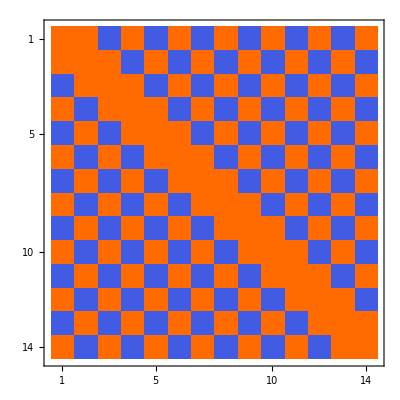

```mathematica
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
```

```mathematica
Print[Style[Sign[ReflectionMatrix[{I,-I,I,-I}]],18,Blue]]
```

{{1,1,-1,1},{1,1,1,-1},{-1,1,1,1},{1,-1,1,1}}

```mathematica
ReflectionMatrix[{I}]//MatrixForm
ReflectionMatrix[{I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]//MatrixForm
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]//MatrixForm
```

(-1)

(0 | 1
1 | 0)

(1/3 | 2/3 | -2/3
2/3 | 1/3 | 2/3
-2/3 | 2/3 | 1/3)

(1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2
-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2)

(3/5 | 2/5 | -2/5 | 2/5 | -2/5
2/5 | 3/5 | 2/5 | -2/5 | 2/5
-2/5 | 2/5 | 3/5 | 2/5 | -2/5
2/5 | -2/5 | 2/5 | 3/5 | 2/5
-2/5 | 2/5 | -2/5 | 2/5 | 3/5)

(2/3 | 1/3 | -1/3 | 1/3 | -1/3 | 1/3
1/3 | 2/3 | 1/3 | -1/3 | 1/3 | -1/3
-1/3 | 1/3 | 2/3 | 1/3 | -1/3 | 1/3
1/3 | -1/3 | 1/3 | 2/3 | 1/3 | -1/3
-1/3 | 1/3 | -1/3 | 1/3 | 2/3 | 1/3
1/3 | -1/3 | 1/3 | -1/3 | 1/3 | 2/3)

(5/7 | 2/7 | -2/7 | 2/7 | -2/7 | 2/7 | -2/7
2/7 | 5/7 | 2/7 | -2/7 | 2/7 | -2/7 | 2/7
-2/7 | 2/7 | 5/7 | 2/7 | -2/7 | 2/7 | -2/7
2/7 | -2/7 | 2/7 | 5/7 | 2/7 | -2/7 | 2/7
-2/7 | 2/7 | -2/7 | 2/7 | 5/7 | 2/7 | -2/7
2/7 | -2/7 | 2/7 | -2/7 | 2/7 | 5/7 | 2/7
-2/7 | 2/7 | -2/7 | 2/7 | -2/7 | 2/7 | 5/7)

(3/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4
1/4 | 3/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | 3/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4
1/4 | -1/4 | 1/4 | 3/4 | 1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4 | 3/4 | 1/4 | -1/4 | 1/4
1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 3/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 3/4 | 1/4
1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 3/4)

(7/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | -2/9
2/9 | 7/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9
-2/9 | 2/9 | 7/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | -2/9
2/9 | -2/9 | 2/9 | 7/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9
-2/9 | 2/9 | -2/9 | 2/9 | 7/9 | 2/9 | -2/9 | 2/9 | -2/9
2/9 | -2/9 | 2/9 | -2/9 | 2/9 | 7/9 | 2/9 | -2/9 | 2/9
-2/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | 7/9 | 2/9 | -2/9
2/9 | -2/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | 7/9 | 2/9
-2/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | -2/9 | 2/9 | 7/9)

(4/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5
1/5 | 4/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5
-1/5 | 1/5 | 4/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5
1/5 | -1/5 | 1/5 | 4/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5
-1/5 | 1/5 | -1/5 | 1/5 | 4/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5
1/5 | -1/5 | 1/5 | -1/5 | 1/5 | 4/5 | 1/5 | -1/5 | 1/5 | -1/5
-1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | 4/5 | 1/5 | -1/5 | 1/5
1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | 4/5 | 1/5 | -1/5
-1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | 4/5 | 1/5
1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | -1/5 | 1/5 | 4/5)

(9/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11
2/11 | 9/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11
-2/11 | 2/11 | 9/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11
2/11 | -2/11 | 2/11 | 9/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11
-2/11 | 2/11 | -2/11 | 2/11 | 9/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11
2/11 | -2/11 | 2/11 | -2/11 | 2/11 | 9/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11
-2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | 9/11 | 2/11 | -2/11 | 2/11 | -2/11
2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | 9/11 | 2/11 | -2/11 | 2/11
-2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | 9/11 | 2/11 | -2/11
2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | 9/11 | 2/11
-2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | -2/11 | 2/11 | 9/11)

(5/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6
1/6 | 5/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6
-1/6 | 1/6 | 5/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6
1/6 | -1/6 | 1/6 | 5/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6
-1/6 | 1/6 | -1/6 | 1/6 | 5/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6
1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 5/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6
-1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 5/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6
1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 5/6 | 1/6 | -1/6 | 1/6 | -1/6
-1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 5/6 | 1/6 | -1/6 | 1/6
1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 5/6 | 1/6 | -1/6
-1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 5/6 | 1/6
1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 5/6)

(11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13
2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13
-2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13
2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13
-2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13
2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13
-2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13
2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13
-2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13 | -2/13
2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13 | 2/13
-2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13 | -2/13
2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13 | 2/13
-2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | -2/13 | 2/13 | 11/13)

(6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7
1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7
-1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7
1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7
-1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7
1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7
-1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7
1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7
-1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7
1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7 | -1/7
-1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7 | 1/7
1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7 | -1/7
-1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7 | 1/7
1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | -1/7 | 1/7 | 6/7)

(13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15
2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15
-2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15
2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15
-2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15
2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15
-2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15
2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15
-2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15
2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15
-2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15 | -2/15
2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15 | 2/15
-2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15 | -2/15
2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15 | 2/15
-2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | -2/15 | 2/15 | 13/15)

(7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8
1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8
-1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8
1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8
-1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8
1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8
-1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8
1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8
-1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8
1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8
-1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8
1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8 | -1/8
-1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8 | 1/8
1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8 | -1/8
-1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8 | 1/8
1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | -1/8 | 1/8 | 7/8)

(15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17
2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17
-2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17
2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17
-2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17
2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17
-2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17
2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17
-2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17
2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17
-2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17
2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17
-2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17 | -2/17
2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17 | 2/17
-2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17 | -2/17
2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17 | 2/17
-2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | -2/17 | 2/17 | 15/17)

(8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9
1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9
-1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9
1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9
-1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9
1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9
-1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9
1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9
-1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9
1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9
-1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9
1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9
-1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9
1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9 | -1/9
-1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9 | 1/9
1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9 | -1/9
-1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9 | 1/9
1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | -1/9 | 1/9 | 8/9)

(17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19 | -2/19
2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19 | 2/19
-2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | -2/19 | 2/19 | 17/19)

(9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10 | -1/10
-1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10 | 1/10
1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | -1/10 | 1/10 | 9/10)

(19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21 | -2/21
2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21 | 2/21
-2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | -2/21 | 2/21 | 19/21)

(10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11 | -1/11
-1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11 | 1/11
1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | -1/11 | 1/11 | 10/11)

(21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23 | -2/23
2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23 | 2/23
-2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | -2/23 | 2/23 | 21/23)

(11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12 | -1/12
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12 | 1/12
1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/12)

(23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25 | -2/25
2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25 | 2/25
-2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | -2/25 | 2/25 | 23/25)

(12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13 | -1/13
-1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13 | 1/13
1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | -1/13 | 1/13 | 12/13)

(25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27 | -2/27
2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27 | 2/27
-2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | -2/27 | 2/27 | 25/27)

(13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14 | -1/14
-1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14 | 1/14
1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | -1/14 | 1/14 | 13/14)

(27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29 | -2/29
2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29 | 2/29
-2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | -2/29 | 2/29 | 27/29)

(14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15 | -1/15
-1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15 | 1/15
1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | -1/15 | 1/15 | 14/15)

(29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31 | -2/31
2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31 | 2/31
-2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | -2/31 | 2/31 | 29/31)

(15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16 | -1/16
-1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16 | 1/16
1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | -1/16 | 1/16 | 15/16)

(31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33 | -2/33
2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33 | 2/33
-2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | -2/33 | 2/33 | 31/33)

(16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17 | -1/17
-1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17 | 1/17
1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | -1/17 | 1/17 | 16/17)

(33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35 | -2/35
2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35 | 2/35
-2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | -2/35 | 2/35 | 33/35)

(17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18 | -1/18
-1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18 | 1/18
1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | -1/18 | 1/18 | 17/18)

```mathematica
Sign[ReflectionMatrix[{I,-I,I,-I}]]
```

{{1,1,-1,1},{1,1,1,-1},{-1,1,1,1},{1,-1,1,1}}

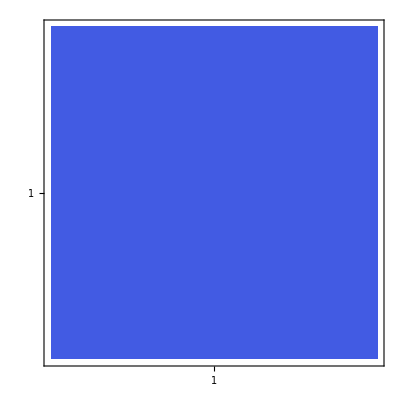

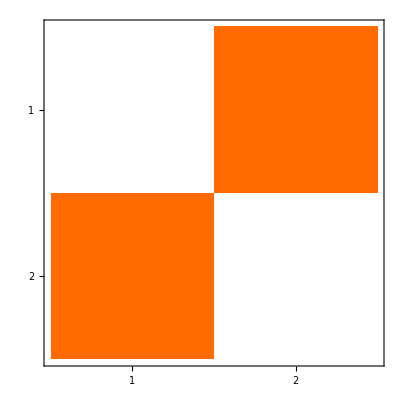

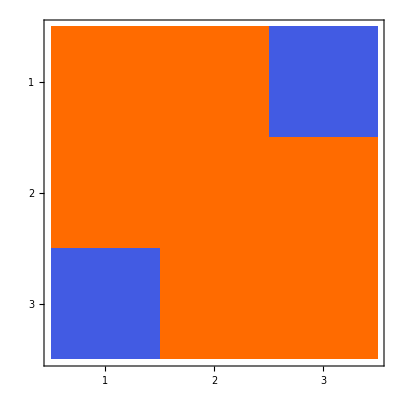

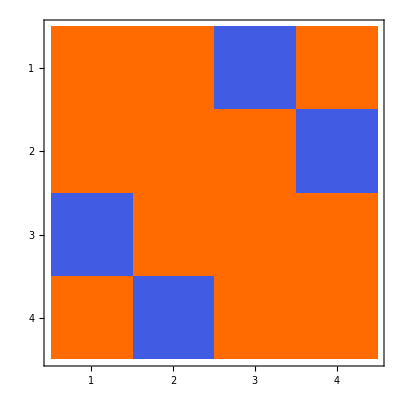

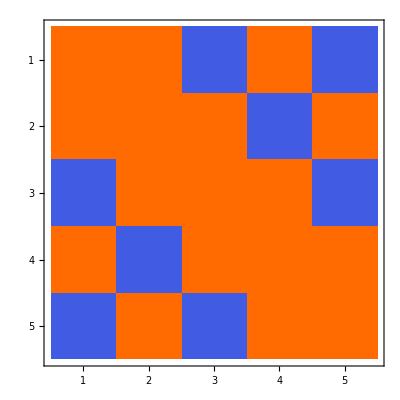

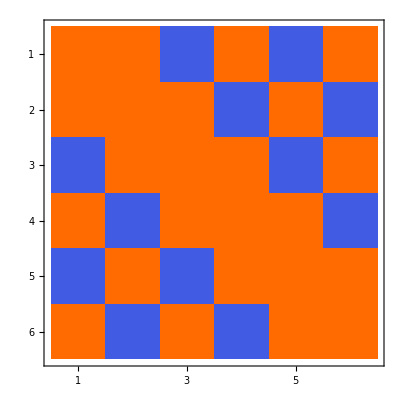

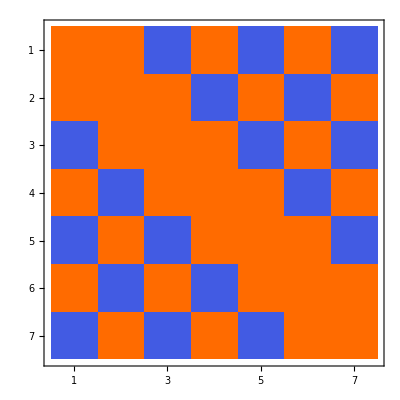

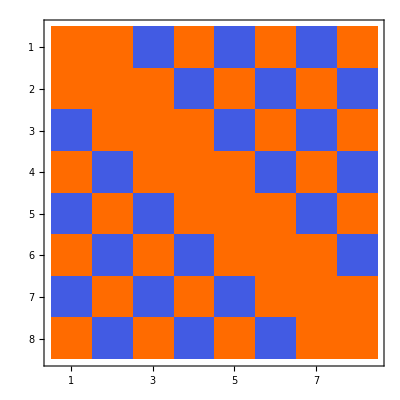

-Graphics-

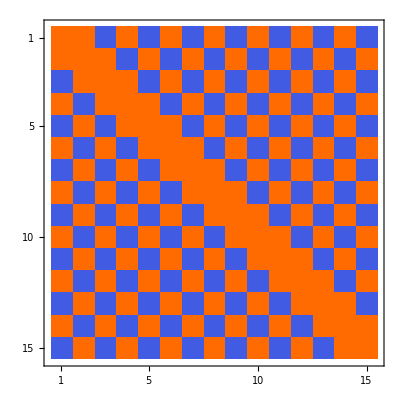

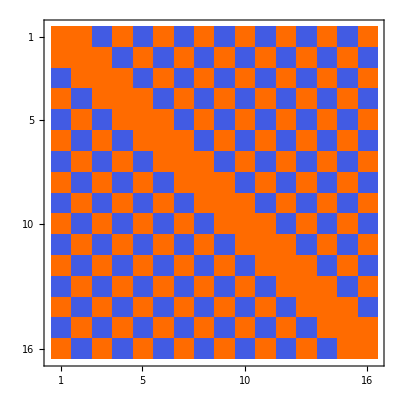

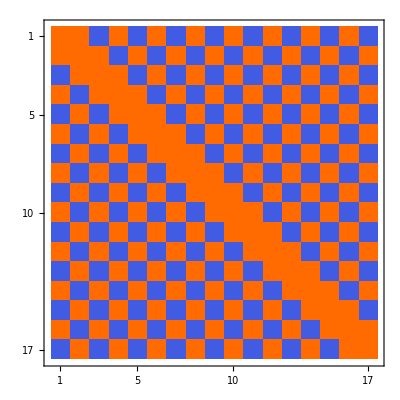

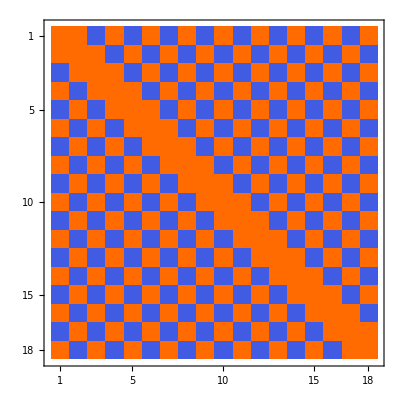

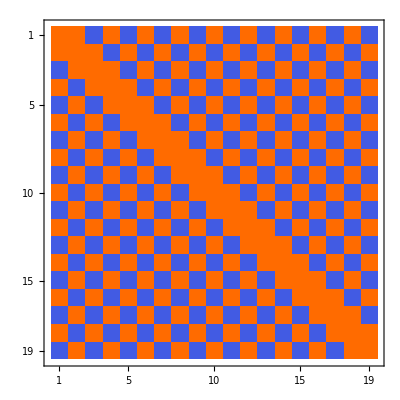

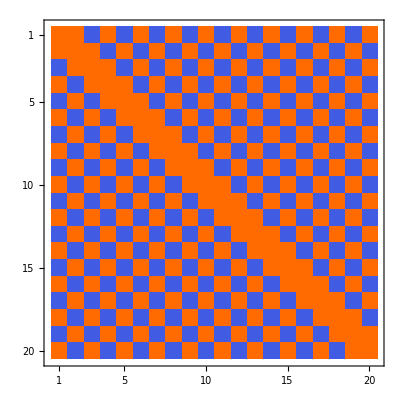

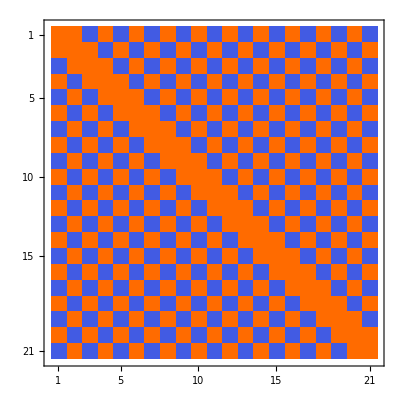

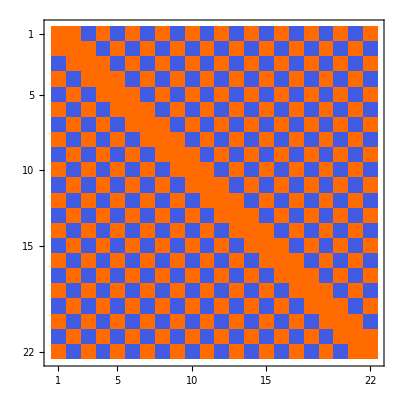

```mathematica
MatrixPlot[Sign[ReflectionMatrix[{I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I}]]]
MatrixPlot[Sign[ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]]]
```

```mathematica
SignTest
```

SignTest

```mathematica
ReflectionMatrix[{I,-I}]
```

{{0,1},{1,0}}

```mathematica
ReflectionMatrix[{{I,-I},{I,-I}}]
```

ReflectionMatrix::inpv: {{ⅈ,-ⅈ},{ⅈ,-ⅈ}} is not a vector.

ReflectionMatrix[{{ⅈ,-ⅈ},{ⅈ,-ⅈ}}]

```mathematica
ReflectionMatrix[{I,-I,I}]
ReflectionMatrix[{I,-I,I,-I}]
```

{{1/3,2/3,-2/3},{2/3,1/3,2/3},{-2/3,2/3,1/3}}

{{1/2,1/2,-1/2,1/2},{1/2,1/2,1/2,-1/2},{-1/2,1/2,1/2,1/2},{1/2,-1/2,1/2,1/2}}

```mathematica
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I}]
```

{{3/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4},{1/4,3/4,1/4,-1/4,1/4,-1/4,1/4,-1/4},{-1/4,1/4,3/4,1/4,-1/4,1/4,-1/4,1/4},{1/4,-1/4,1/4,3/4,1/4,-1/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4,3/4,1/4,-1/4,1/4},{1/4,-1/4,1/4,-1/4,1/4,3/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4,-1/4,1/4,3/4,1/4},{1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,3/4}}

```mathematica
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]
```

{{7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8},{1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8},{-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8},{1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8},{-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8},{1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8},{-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8},{1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8},{-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8},{1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8,-1/8},{-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8,1/8},{1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8,-1/8},{-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8,1/8},{1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8,-1/8},{-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8,1/8},{1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,-1/8,1/8,7/8}}

```mathematica
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]
```

{{15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16,-1/16},{-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16,1/16},{1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,-1/16,1/16,15/16}}

```mathematica
{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}.ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I,I,-I}]
```

{-ⅈ,ⅈ,-ⅈ,ⅈ,-ⅈ,ⅈ,-ⅈ,ⅈ,-ⅈ,ⅈ,-ⅈ,ⅈ,-ⅈ,ⅈ,-ⅈ,ⅈ}

```mathematica
ReflectionMatrix[{-I}]
ReflectionMatrix[{1}]
ReflectionMatrix[{I}]

ReflectionMatrix[{I,-I}]
ReflectionMatrix[{I,-I,I,-I}]

ReflectionMatrix[{{I,-I}. {I,-I}}]
ReflectionMatrix[{{I,-I} .{I,-I}. {I,-I}}]
FullSimplify[ReflectionMatrix[{{I,-I} .{I,-I}. {I,-I}}]]
ReflectionMatrix[{{I,-I} .{I,-I}. {I,-I}. {I,-I}}]
FullSimplify[ReflectionMatrix[{{I,-I} .{I,-I}. {I,-I}. {I,-I}}]]
ReflectionMatrix[{{I,-I} .{I,-I}. {I,-I}. {I,-I}. {I,-I}}]
FullSimplify[ReflectionMatrix[{{I,-I} .{I,-I}. {I,-I}. {I,-I}. {I,-I}}]]

ReflectionMatrix[{I,I,I}]
ReflectionMatrix[{I,I,I,I}]
ReflectionMatrix[{I,I,I,I,I}]
ReflectionMatrix[{I,I,I,I,I,I}]

ReflectionMatrix[{I,-I,I,-I,I,-I}]
ReflectionMatrix[{I,-I,I,-I,I,-I,I,-I}]
```

{{-1}}

{{-1}}

{{-1}}

{{0,1},{1,0}}

{{1/2,1/2,-1/2,1/2},{1/2,1/2,1/2,-1/2},{-1/2,1/2,1/2,1/2},{1/2,-1/2,1/2,1/2}}

{{-1}}

{{1-(2 Conjugate[(-2).{ⅈ,-ⅈ}] (-2).{ⅈ,-ⅈ})/Abs[(-2).{ⅈ,-ⅈ}]^2}}

{{-1}}

{{1-(2 Conjugate[(-2).(-2)] (-2).(-2))/Abs[(-2).(-2)]^2}}

{{-1}}

{{1-(2 Conjugate[(-2).(-2).{ⅈ,-ⅈ}] (-2).(-2).{ⅈ,-ⅈ})/Abs[(-2).(-2).{ⅈ,-ⅈ}]^2}}

{{-1}}

{{1/3,-2/3,-2/3},{-2/3,1/3,-2/3},{-2/3,-2/3,1/3}}

{{1/2,-1/2,-1/2,-1/2},{-1/2,1/2,-1/2,-1/2},{-1/2,-1/2,1/2,-1/2},{-1/2,-1/2,-1/2,1/2}}

{{3/5,-2/5,-2/5,-2/5,-2/5},{-2/5,3/5,-2/5,-2/5,-2/5},{-2/5,-2/5,3/5,-2/5,-2/5},{-2/5,-2/5,-2/5,3/5,-2/5},{-2/5,-2/5,-2/5,-2/5,3/5}}

{{2/3,-1/3,-1/3,-1/3,-1/3,-1/3},{-1/3,2/3,-1/3,-1/3,-1/3,-1/3},{-1/3,-1/3,2/3,-1/3,-1/3,-1/3},{-1/3,-1/3,-1/3,2/3,-1/3,-1/3},{-1/3,-1/3,-1/3,-1/3,2/3,-1/3},{-1/3,-1/3,-1/3,-1/3,-1/3,2/3}}

{{2/3,1/3,-1/3,1/3,-1/3,1/3},{1/3,2/3,1/3,-1/3,1/3,-1/3},{-1/3,1/3,2/3,1/3,-1/3,1/3},{1/3,-1/3,1/3,2/3,1/3,-1/3},{-1/3,1/3,-1/3,1/3,2/3,1/3},{1/3,-1/3,1/3,-1/3,1/3,2/3}}

{{3/4,1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4},{1/4,3/4,1/4,-1/4,1/4,-1/4,1/4,-1/4},{-1/4,1/4,3/4,1/4,-1/4,1/4,-1/4,1/4},{1/4,-1/4,1/4,3/4,1/4,-1/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4,3/4,1/4,-1/4,1/4},{1/4,-1/4,1/4,-1/4,1/4,3/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4,-1/4,1/4,3/4,1/4},{1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,3/4}}

```mathematica
FullSimplify[2 Conjugate[(-2).(-2).{ⅈ,-ⅈ}] (-2).(-2).{ⅈ,-ⅈ}]
```

2 Abs[(-2).(-2).{ⅈ,-ⅈ}]^2

```mathematica
2 Abs[(-2).(-2).{ⅈ,-ⅈ}]^2 /Abs[(-2).(-2).{ⅈ,-ⅈ}]^2
```

2

```mathematica
FullSimplify[2 Abs[(-2).(-2).{ⅈ,-ⅈ}]^2] //N
```

2. Abs[(-2.).(-2.).{0.+1. ⅈ,0.-1. ⅈ}]^2

```mathematica
Abs[(-2).(-2).{ⅈ,-ⅈ}]^2
```

Abs[(-2).(-2).{ⅈ,-ⅈ}]^2

```mathematica
2. Abs[(-2.).(-2.).{0.+1. ⅈ,0.-1. ⅈ}]^2
```

2.  Abs[(-2.).(-2.).{0.+1. ⅈ,0.-1. ⅈ}]^2

```mathematica
ReflectionMatrix[{I,-I}]//MatrixForm
ReflectionMatrix[{-I,I}]//MatrixForm
ReflectionMatrix[{I,I}]//MatrixForm
ReflectionMatrix[{-I,-I}]//MatrixForm
```

(0 | 1
1 | 0)

(0 | 1
1 | 0)

(0 | -1
-1 | 0)

(0 | -1
-1 | 0)

```mathematica
Dot[{I,Conjugate[I]}, {I,Conjugate[I]}]
Cross[{I,Conjugate[I]}, {I,Conjugate[I]}]
Inner[{I,Conjugate[I]}, {I,Conjugate[I]}]
Outer[{I,Conjugate[I]}, {I,Conjugate[I]}]
```

-2

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{ⅈ,-ⅈ}×{ⅈ,-ⅈ}

Inner::argb: Inner called with 2 arguments; between 3 and 5 arguments are expected.

Inner[{ⅈ,-ⅈ},{ⅈ,-ⅈ}]

{{ⅈ,-ⅈ}[ⅈ],{ⅈ,-ⅈ}[-ⅈ]}

```mathematica
Reverse[{{ⅈ,-ⅈ}[ⅈ],{ⅈ,-ⅈ}[-ⅈ]}]
```

{{ⅈ,-ⅈ}[-ⅈ],{ⅈ,-ⅈ}[ⅈ]}

```mathematica
Outer[{I,Conjugate[I]}, {I,Conjugate[I]}]
```

{{ⅈ,-ⅈ}[ⅈ],{ⅈ,-ⅈ}[-ⅈ]}

```mathematica
Outer[%]
```

Outer::argmu: Outer called with 1 argument; 2 or more arguments are expected.

Outer[{{ⅈ,-ⅈ}[ⅈ],{ⅈ,-ⅈ}[-ⅈ]}]

```mathematica
Dot[{I,Conjugate[I]}, {I,Conjugate[I]}, {I,Conjugate[I]}, {I,Conjugate[I]}]
FullSimplify[Dot[{I,Conjugate[I]}, {I,Conjugate[I]}, {I,Conjugate[I]}, {I,Conjugate[I]}]]//N
```

(-2).(-2)

(-2.).(-2.)

```mathematica
(-2.).(-2.)
```

(-2.).(-2.)

```mathematica
ReflectionMatrix[{0}]
```

ReflectionMatrix::idir: Direction vector {0} has zero magnitude.

ReflectionMatrix[{0}]

```mathematica
ζ0=0
ζ1=-I
```

0

-ⅈ

```mathematica
Solve[{x1^2 ==0,x1 == ζ0^2 - ζ1^2},{ζ0,ζ1}]
```

Solve::ivar: 0 is not a valid variable.

```mathematica
ζ0^2
```

0

```mathematica
ζ1^2
```

-1

```mathematica
ζ1^2^2
```

1

```mathematica
Solve[{x1^2+x2^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == (*I*)x1(ζ0^2 + ζ1^2)}]
```

{}

```mathematica
Solve[{x1^2+x2^2+x3^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2},{ζ0,ζ1}]
```

Solve::ivar: 0 is not a valid variable.

Solve[{x1^2+x2^2+x3^2==0,x1==1,x2==-ⅈ,x3==0},{0,ⅈ}]

```mathematica
Solve[{x1^2+x2^2+x3^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2}]
```

{{x1→-ζ1^2,x2→ⅈ ζ1^2,x3→0,ζ0→0},{x1→ζ0^2,x2→ⅈ ζ0^2,x3→0,ζ1→0},{x1→(-1+ζ0^4)/ζ0^2,x2→(ⅈ (1+ζ0^4))/ζ0^2,x3→-2,ζ1→-1/ζ0},{x1→(-1+ζ0^4)/ζ0^2,x2→(ⅈ (1+ζ0^4))/ζ0^2,x3→-2,ζ1→1/ζ0}}

```mathematica
Reduce[{x1^2+x2^2+x3^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2},{ζ0,ζ1}]
```

(x3==-2||x3==0)&&(x1==-√(-x2^2+2 x3)||x1==√(-x2^2+2 x3))&&(ζ0==-(√(x1-ⅈ x2))/(√2)||ζ0==(√(x1-ⅈ x2))/(√2))&&(ζ1==-(√(-x1-ⅈ x2))/(√2)||ζ1==(√(-x1-ⅈ x2))/(√2))

```mathematica
Reduce[{x1^2+x2^2+x3^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2}]
```

(ζ1==0&&x3==0&&x2==ⅈ ζ0^2&&x1==ζ0^2)||(ζ1≠0&&(ζ0==0||ζ0==-1/ζ1||ζ0==1/ζ1)&&x3==-2 ζ0^2 ζ1^2&&x2==ⅈ (ζ0^2+ζ1^2)&&x1==ζ0^2-ζ1^2)

```mathematica
Reduce[{x1^2+x2^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2)}]
```

(ζ1==0&&x2==ⅈ ζ0^2&&x1==ζ0^2)||(ζ1≠0&&ζ0==0&&x2==ⅈ ζ1^2&&x1==-ζ1^2)

```mathematica
Reduce[{x1^2==0,x1 == ζ0^2 - ζ1^2}]
```

(ζ0==-ζ1||ζ0==ζ1)&&x1==0

```mathematica
ζ0 =(1/2I)
Reduce[{x1^2==0,x1 == ζ0^2 - ζ1^2}]
Clear[ζ0]
```

ⅈ/2

(ζ1==-ⅈ/2||ζ1==ⅈ/2)&&x1==0

```mathematica
ζ0 =(1/(2I))
Reduce[{x1^2==0,x1 == ζ0^2 - ζ1^2}]
Clear[ζ0]
```

-ⅈ/2

(ζ1==-ⅈ/2||ζ1==ⅈ/2)&&x1==0

```mathematica
ζ0 =-I
Reduce[{x1^2==0,x1 == ζ0^2 - ζ1^2}]
1Clear[ζ0]
```

-ⅈ

(ζ1==-ⅈ||ζ1==ⅈ)&&x1==0

```mathematica
Solve[{x1^2+x2^2+x3^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2}]
```

{{x1→-ζ1^2,x2→ⅈ ζ1^2,x3→0,ζ0→0},{x1→ζ0^2,x2→ⅈ ζ0^2,x3→0,ζ1→0},{x1→(-1+ζ0^4)/ζ0^2,x2→(ⅈ (1+ζ0^4))/ζ0^2,x3→-2,ζ1→-1/ζ0},{x1→(-1+ζ0^4)/ζ0^2,x2→(ⅈ (1+ζ0^4))/ζ0^2,x3→-2,ζ1→1/ζ0}}

```mathematica
Solve[{x1^2+x2^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2)}]
```

{{x1→-ζ1^2,x2→ⅈ ζ1^2,ζ0→0},{x1→ζ0^2,x2→ⅈ ζ0^2,ζ1→0}}

```mathematica
Solve[{x1^2 ==0,x1 == ζ0^2 - ζ1^2}]
```

{{x1→0,ζ1→-ζ0},{x1→0,ζ1→ζ0}}

Spinor

Using Cartans nomenclature ζ0, ζ1, x1, x2, x3

```mathematica
Clear[ζ0,ζ1,x1, X2,x3]
```

Single inserted value thus single assumption: ζ0 = I a Complex Entity that is not NULL

```mathematica
ζ0 =I
```

ⅈ

Take Conjugate ζ0 as ‘Hole’ in or ‘Shadow on the NULL Plane by existence of ζ0
Genitive value reflecting lack of: ζ0 + Conjugate[ζ0] must sum to NULL 
Core of symmetry 
Mathematically a Reflection thus a Rotation.

```mathematica
ζ1=Conjugate[ζ0] 
ζ0 + ζ1
```

-ⅈ

0

x1 defines the NULL Plane

```mathematica
x1 = ζ0^2 - ζ1^2 
ζ0^2
ζ1^2
x1
```

0

-1

-1

0

```mathematica
x2 = I(ζ0^2 + ζ1^2)
ζ0^2
ζ1^2
x2
```

-2 ⅈ

-1

-1

-2 ⅈ

```mathematica
x3 = -2ζ0^2ζ1^2
ζ0^2
ζ1^2
x3
```

-2

-1

-1

-2

```mathematica
x1^2 + x2^2 + x3^2 
x1
x1^2
x2
x2^2
x3
x3^2
```

0

0

0

-2 ⅈ

-4

-2

4

```mathematica
Clear[ζ0,ζ1,x1, X2,x3]
```

```mathematica
ζ0 =I
```

ⅈ

```mathematica
ζ1=Conjugate[I]
```

-ⅈ

```mathematica
x1 = ζ0^2 - ζ1^2 
ζ0^2
ζ1^2
x1
ζ0
ζ1
```

0

-1

-1

0

ⅈ

-ⅈ

```mathematica
x2 = I(ζ0^2 + ζ1^2)
ζ0^2
ζ1^2
x2
ζ0
ζ1
```

-2 ⅈ

-1

-1

-2 ⅈ

ⅈ

-ⅈ

```mathematica
x3 = -2ζ0^2ζ1^2
ζ0^2
ζ1^2
x3
ζ0
ζ1
```

-2

-1

-1

-2

ⅈ

-ⅈ

```mathematica
With[{n=Abs[2],a=Arg[2]},Defer[n ⅇ^(ⅈ a)]]
```

2 ⅇ^(ⅈ 0)

```mathematica
2 ⅇ^(ⅈ 0)
```

2

```mathematica
With[{n=Abs[-2],a=Arg[-2]},Defer[n ⅇ^(ⅈ a)]]
```

2 ⅇ^(ⅈ π)

```mathematica
With[{n=Abs[1],a=Arg[1]},Defer[n ⅇ^(ⅈ a)]]
```

1 ⅇ^(ⅈ 0)

```mathematica
With[{n=Abs[-1],a=Arg[-1]},Defer[n ⅇ^(ⅈ a)]]
```

1 ⅇ^(ⅈ π)

```mathematica
ConvertToEx-1
```

-1+ConvertToEx

```mathematica
IntegerPart[ⅈ]
```

ⅈ

```mathematica
Conjugate[ⅈ]
```

-ⅈ

```mathematica
IntegerPart[-ⅈ]
```

-ⅈ

```mathematica
Round[-ⅈ]
```

-ⅈ

```mathematica
MinimalPolynomial[-ⅈ,x]
```

1+x^2

```mathematica
AlgebraicNumberNorm[-ⅈ]
```

1

```mathematica
Abs[ⅈ]
```

1

```mathematica
BaseForm[1,2]
```

1_2

```mathematica
BaseForm[4,2]
```

100_2

```mathematica
BaseForm[4ⅈ,2]
```

100_2 ⅈ

```mathematica
BaseForm[ⅈ,1]
```

BaseForm::basf: Requested base 1 should be an integer between 2 and 36.

BaseForm[ⅈ,1]

```mathematica
Function
```

```mathematica
Sin[1/4 Pi]
```

1/(√2)

```mathematica
"convert to exponential"ⅈWith[{n=Abs[ⅈ],a=Arg[ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

1 ⅇ^((ⅈ π)/2)

```mathematica
"convert to exponential"-ⅈWith[{n=Abs[-ⅈ],a=Arg[-ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

1 ⅇ^(1/2 ⅈ (-π))

```mathematica
x1^2 + x2^2 + x3^2 
x1
x1^2
x2
x2^2
x3
x3^2
ζ0
ζ1
```

0

0

0

-2 ⅈ

-4

-2

4

ⅈ

-ⅈ

```mathematica
ζ0
ζ1
```

ⅈ

-ⅈ

```mathematica
ζ0/ζ1
ζ0
ζ1
```

-1

ⅈ

-ⅈ

Plot of Spinor values so far.

```mathematica
Graphics3D[{Gray,PointSize->.04,{Point[{0,0,0}]},
{Red,PointSize->.08,Point[{1,0,0}],Point[{0,-2,0}]},
{Pink,PointSize->.08,Point[{-1,0,0}]},
{Brown,PointSize->.06,Point[{0,-2,0}]},
{Pink,PointSize->.08,Point[{0,-2,-2}]},
{LightBlue,PointSize->.06,Point[{0,-2,-2}]},
{Gray,PointSize->.04,Point[{0,-2,-1}]},}]
```

-Graphics3D-

```mathematica
Show[%9,ViewPoint->{-∞,0,0}]
```

Show::gcomb: Could not combine the graphics objects in Show[{{0,1},{1,0}},ViewPoint→{-∞,0,0}].

Show[{{0,1},{1,0}},ViewPoint→{-∞,0,0}]

```mathematica
Graphics3D[{Gray,PointSize->.04,{Point[{0,0,0}]},{Pink,PointSize->.08,Point[{1,0,0}],Point[{0,-2,0}]},{LightPink,PointSize->.08,Point[{-1,0,0}]},{Brown,PointSize->.06,Point[{0,-2,0}]}}]
```

-Graphics3D-

```mathematica
Graphics3D[{Gray,PointSize->.04,{Point[{0,0,0}]},{Pink,PointSize->.08,Point[{1,0,0}],Point[{0,-2,0}]},{LightPink,PointSize->.08,Point[{-1,0,0}]},{Brown,PointSize->.06,Point[{0,-2,0}]}}]
```

-Graphics3D-

```mathematica
Graphics3D[{Black,PointSize->.1,{Point[{0,0,0}]},{Purple,PointSize->.08,Point[{1,0,0}],Point[{-1,0,0}],Point[{0,-2,0}]},{Red,PointSize->.06,Point[{0,0,-2}]}}]
```

-Graphics3D-

```mathematica
Graphics3D[{Blue,PointSize->.1,{Point[{1,0,0}],Point[{-1,0,0}],Point[{0,1,0}],Point[{0,-1,0}],Point[{0,0,1}],Point[{0,0,-1}],{Red,PointSize->.06,Point[{0,0,0}]},{Blue,PointSize->.01,{Line[{{-1,0,0},{1,0,0}}],Line[{{0,-1,0},{0,1,0}}],Line[{{0,0,-1},{0,0,1}}]}
}}}]
```

-Graphics3D-

Single inserted value thus single assumption: ζ0 = I a Complex Unity that is not NULL
1st calculated value from single assumption in terms of I from x2 = -2I taking ‘-‘ to be the Conjugate of I --- fails as X^2  not = zero

```mathematica
Clear[ζ0,ζ1,x1,x2,x3]
```

```mathematica
ζ0 =Conjugate[I]
```

-ⅈ

```mathematica
ζ1=Conjugate[ζ0]
```

ⅈ

```mathematica
ζ0 =1
```

1

```mathematica
ζ0 =0
```

0

```mathematica
x1 = ζ0^2 - ζ1^2 
ζ0^2
ζ1^2
x1
ζ0
ζ1
```

1

0

-1

1

0

ⅈ

```mathematica
x2 = I(ζ0^2 + ζ1^2)
ζ0^2
ζ1^2
x2
ζ0
ζ1
```

-ⅈ

0

-1

-ⅈ

0

ⅈ

```mathematica
x3 = -2ζ0^2ζ1^2
ζ0^2
ζ1^2
x3
ζ0
ζ1
```

0

0

-1

0

0

ⅈ

```mathematica
x1^2 + x2^2 + x3^2 
x1
x1^2
x2
x2^2
x3
x3^2
ζ0
ζ1
```

0

1

1

-ⅈ

-1

0

0

0

ⅈ

```mathematica
ζ0
ζ1
```

0

ⅈ

```mathematica
ζ0/ζ1
ζ0
ζ1
```

0

0

ⅈ

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Im[x1],0,0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,Im[ζ1],0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,Im[ζ0],0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,0,Im[ζ1]}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,0,Im[ζ0]}]}

},PlotLabel->Complex]
```

-Graphics3D-

```mathematica
Array[a,{1,2,4,8}]
```

{{{{a[1,1,1,1],a[1,1,1,2],a[1,1,1,3],a[1,1,1,4],a[1,1,1,5],a[1,1,1,6],a[1,1,1,7],a[1,1,1,8]},{a[1,1,2,1],a[1,1,2,2],a[1,1,2,3],a[1,1,2,4],a[1,1,2,5],a[1,1,2,6],a[1,1,2,7],a[1,1,2,8]},{a[1,1,3,1],a[1,1,3,2],a[1,1,3,3],a[1,1,3,4],a[1,1,3,5],a[1,1,3,6],a[1,1,3,7],a[1,1,3,8]},{a[1,1,4,1],a[1,1,4,2],a[1,1,4,3],a[1,1,4,4],a[1,1,4,5],a[1,1,4,6],a[1,1,4,7],a[1,1,4,8]}},{{a[1,2,1,1],a[1,2,1,2],a[1,2,1,3],a[1,2,1,4],a[1,2,1,5],a[1,2,1,6],a[1,2,1,7],a[1,2,1,8]},{a[1,2,2,1],a[1,2,2,2],a[1,2,2,3],a[1,2,2,4],a[1,2,2,5],a[1,2,2,6],a[1,2,2,7],a[1,2,2,8]},{a[1,2,3,1],a[1,2,3,2],a[1,2,3,3],a[1,2,3,4],a[1,2,3,5],a[1,2,3,6],a[1,2,3,7],a[1,2,3,8]},{a[1,2,4,1],a[1,2,4,2],a[1,2,4,3],a[1,2,4,4],a[1,2,4,5],a[1,2,4,6],a[1,2,4,7],a[1,2,4,8]}}}}

```mathematica
Array[count,{1,2,4,8}]//MatrixForm
```

((count[1,1,1,1] | count[1,1,1,2] | count[1,1,1,3] | count[1,1,1,4] | count[1,1,1,5] | count[1,1,1,6] | count[1,1,1,7] | count[1,1,1,8]
count[1,1,2,1] | count[1,1,2,2] | count[1,1,2,3] | count[1,1,2,4] | count[1,1,2,5] | count[1,1,2,6] | count[1,1,2,7] | count[1,1,2,8]
count[1,1,3,1] | count[1,1,3,2] | count[1,1,3,3] | count[1,1,3,4] | count[1,1,3,5] | count[1,1,3,6] | count[1,1,3,7] | count[1,1,3,8]
count[1,1,4,1] | count[1,1,4,2] | count[1,1,4,3] | count[1,1,4,4] | count[1,1,4,5] | count[1,1,4,6] | count[1,1,4,7] | count[1,1,4,8]) | (count[1,2,1,1] | count[1,2,1,2] | count[1,2,1,3] | count[1,2,1,4] | count[1,2,1,5] | count[1,2,1,6] | count[1,2,1,7] | count[1,2,1,8]
count[1,2,2,1] | count[1,2,2,2] | count[1,2,2,3] | count[1,2,2,4] | count[1,2,2,5] | count[1,2,2,6] | count[1,2,2,7] | count[1,2,2,8]
count[1,2,3,1] | count[1,2,3,2] | count[1,2,3,3] | count[1,2,3,4] | count[1,2,3,5] | count[1,2,3,6] | count[1,2,3,7] | count[1,2,3,8]
count[1,2,4,1] | count[1,2,4,2] | count[1,2,4,3] | count[1,2,4,4] | count[1,2,4,5] | count[1,2,4,6] | count[1,2,4,7] | count[1,2,4,8]))

```mathematica
Transpose[ Array[count,{1,2,4,8}]]//MatrixForm
```

((count[1,1,1,1] | count[1,1,1,2] | count[1,1,1,3] | count[1,1,1,4] | count[1,1,1,5] | count[1,1,1,6] | count[1,1,1,7] | count[1,1,1,8]
count[1,1,2,1] | count[1,1,2,2] | count[1,1,2,3] | count[1,1,2,4] | count[1,1,2,5] | count[1,1,2,6] | count[1,1,2,7] | count[1,1,2,8]
count[1,1,3,1] | count[1,1,3,2] | count[1,1,3,3] | count[1,1,3,4] | count[1,1,3,5] | count[1,1,3,6] | count[1,1,3,7] | count[1,1,3,8]
count[1,1,4,1] | count[1,1,4,2] | count[1,1,4,3] | count[1,1,4,4] | count[1,1,4,5] | count[1,1,4,6] | count[1,1,4,7] | count[1,1,4,8])
(count[1,2,1,1] | count[1,2,1,2] | count[1,2,1,3] | count[1,2,1,4] | count[1,2,1,5] | count[1,2,1,6] | count[1,2,1,7] | count[1,2,1,8]
count[1,2,2,1] | count[1,2,2,2] | count[1,2,2,3] | count[1,2,2,4] | count[1,2,2,5] | count[1,2,2,6] | count[1,2,2,7] | count[1,2,2,8]
count[1,2,3,1] | count[1,2,3,2] | count[1,2,3,3] | count[1,2,3,4] | count[1,2,3,5] | count[1,2,3,6] | count[1,2,3,7] | count[1,2,3,8]
count[1,2,4,1] | count[1,2,4,2] | count[1,2,4,3] | count[1,2,4,4] | count[1,2,4,5] | count[1,2,4,6] | count[1,2,4,7] | count[1,2,4,8]))

```mathematica
-
```

```mathematica
{a,{b,Congruent[b]},{{c,Congruent[c],{d,Congruent[d]},{e,Congruent[e]},{f,Congruent[f]}}}}//MatrixForm
```

(a
{b,Congruent[b]}
{{c,Congruent[c],{d,Congruent[d]},{e,Congruent[e]},{f,Congruent[f]}}})

```mathematica
{a,{b,Congruent[b]},{{b,Congruent[b],{b,Congruent[b]},{b,Congruent[b]},{b,Congruent[b]}}}}//MatrixForm
```

(a
{b,Congruent[b]}
{{b,Congruent[b],{b,Congruent[b]},{b,Congruent[b]},{b,Congruent[b]}}})

```mathematica
Transpose[ {a,{b,Congruent[b]},{{c,Congruent[c],{d,Congruent[d]},{e,Congruent[e]},{f,Congruent[f]}}}}]//MatrixForm
```

Transpose::nmtx: The first two levels of {a,{b,Congruent[b]},{{c,Congruent[c],{d,Congruent[d]},{e,Congruent[e]},{f,Congruent[f]}}}} cannot be transposed.

Transpose[{a,{b,Congruent[b]},{{c,Congruent[c],{d,Congruent[d]},{e,Congruent[e]},{f,Congruent[f]}}}}]

```mathematica
Congruent[Null]
```

Congruent[Null]

```mathematica
Simplify[Congruent[Null]]
```

Congruent[Null]

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Re[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Re[ζ1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Re[x1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Re[x2],0,0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,Re[-I],0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,Re[I],0}]}
},PlotLabel->Real]
```

-Graphics3D-

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Im[x1],0,0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,Im[ζ1],0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,Im[ζ0],0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,0,Im[ζ1]}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,0,Im[ζ0]}]}

},PlotLabel->Complex]
```

-Graphics3D-

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Im[x1],0,0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,Im[ζ1],0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,Im[ζ0],0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,0,Im[ζ1]}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,0,Im[ζ0]}]}

},PlotLabel->Complex]
```

-Graphics3D-

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Im[x1],0,0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,Im[ζ1],0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,Im[ζ0],0}]},
{RGBColor[0.5,0,0],PointSize->.08,Point[{0,0,Im[ζ1]}]},
{RGBColor[1,0,0],PointSize->.08,Point[{0,0,Im[ζ0]}]}

},PlotLabel->Complex]
```

-Graphics3D-

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Arrow[{{0,0,0},{0,Im[ζ0],0}}]}(*{RGBColor[0.5,0,0],PointSize->.08,Arrow[{Im[ζ1],0}]}
{RGBColor[0,1,0],PointSize->.08,Arrow[{Im[x1],0}]},
{RGBColor[0.5,0,0],PointSize->.08,Arrow[{0,Im[ζ1]}]},
{RGBColor[1,0,0],PointSize->.08,Arrow[{0,Im[ζ0]}]},
{RGBColor[0.5,0,0],PointSize->.08,Arrow[{0,Im[ζ1]}]},
{RGBColor[1,0,0],PointSize->.08,Arrow[{0,Im[ζ0]}]}
*)
},PlotLabel->Complex]
```

-Graphics3D-

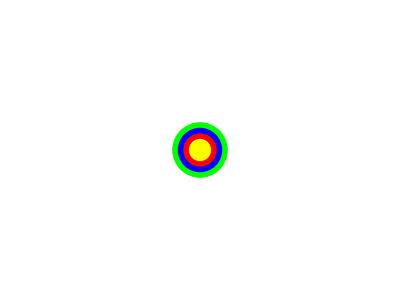

```mathematica
Graphics[{{Green,PointSize->.10,Point[{0,0}]},{Blue,PointSize->.08,Point[{0,0}]},{Red,PointSize->.06,Point[{0,0}]},{Yellow,PointSize->.04,Point[{0,0}]}}]
```

```mathematica
Graphics3D[{{Green,PointSize->.1,{Point[{1,0,0}]},{Darker[Green],PointSize->.1,{Point[{-1,0,0}]}},{Blue,PointSize->.1,{Point[{0,1,0}]}},{Darker[Blue],PointSize->.1,{Point[{0,-1,0}]}},{Red,PointSize->.1,{Point[{0,0,1}]}},{Darker[Red],PointSize->.1,{Point[{0,0,-1}]}},(*{Red,PointSize->.06,Point[{0,0,0}]}*){{Green,PointSize->.10,Point[{0,0,0}]},{Blue,PointSize->.08,Point[{0,0,0}]},{Red,PointSize->.06,Point[{0,0,0}]},{Yellow,PointSize->.04,Point[{0,0,0}]}},{Green,PointSize->.01,{Line[{{-1,0,0},{1,0,0}}]}},{Blue,PointSize->.01,{Line[{{0,-1,0},{0,1,0}}]}},{Line[{{0,0,-1},{0,0,1}}]}}
}]
```

-Graphics3D-

```mathematica
{{0},{1}}
% //MatrixForm
```

{{0},{1}}

(0
1)

```mathematica
ReflectionMatrix[{{0},{1}}]
% //MatrixForm
```

ReflectionMatrix::inpv: {{0},{1}} is not a vector.

ReflectionMatrix[{{0},{1}}]

ReflectionMatrix[{{0},{1}}]

```mathematica
ReflectionMatrix[{0,1}]
% //MatrixForm
```

{{1,0},{0,-1}}

(1 | 0
0 | -1)

```mathematica
ReflectionMatrix[{1,0}]
% //MatrixForm
```

{{-1,0},{0,1}}

(-1 | 0
0 | 1)

```mathematica
ReflectionMatrix[{{1},{0}}]
% //MatrixForm
```

ReflectionMatrix::inpv: {{1},{0}} is not a vector.

ReflectionMatrix[{{1},{0}}]

ReflectionMatrix[{{1},{0}}]

```mathematica
Graphics[{Gray,PointSize->.10,{Point[{0,0}]},
{RGBColor[1,0],PointSize->.08,Point[{Im[ζ0],0]},{RGBColor[0.5,0],PointSize->.08,Point[{Im[ζ1],0}]}

},PlotLabel->Complex]
```

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{0,Im[ζ0],0}]},{RGBColor[0,0.5,0],PointSize->.08,Point[{0,Im[ζ1],0}]}

},PlotLabel->Complex]


Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[0,0,1],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0,0,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[0,1,1],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0,0.5,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,1,0],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.5,0.5,0],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[0.5,1,0.5],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.25,0.5,0.25],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0.5,0],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.5,0.25,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]


Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0.5,1],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.5,0.25,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«5 more identical outputs»

```mathematica
{{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]}}
```

{{ⅈ,Congruent[ⅈ]},{ⅈ,Congruent[ⅈ]},{ⅈ,Congruent[ⅈ]},{ⅈ,Congruent[ⅈ]},{ⅈ,Congruent[ⅈ]},{ⅈ,Congruent[ⅈ]},{ⅈ,Congruent[ⅈ]},{ⅈ,Congruent[ⅈ]}}

```mathematica
{{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]},{I,Congruent[I]}}//MatrixForm
```

(ⅈ | Congruent[ⅈ]
ⅈ | Congruent[ⅈ]
ⅈ | Congruent[ⅈ]
ⅈ | Congruent[ⅈ]
ⅈ | Congruent[ⅈ]
ⅈ | Congruent[ⅈ]
ⅈ | Congruent[ⅈ]
ⅈ | Congruent[ⅈ])

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},

{Gray,PointSize->.10,Point[{0,0,1}]},
{RGBColor[0,1,0],PointSize->.08,Point[{0,Im[ζ0],1}]},{RGBColor[0,0.5,0],PointSize->.08,Point[{0,Im[ζ1],1}]}

},PlotLabel->Complex]


Graphics3D[{Gray,PointSize->.10,{Point[{2,0,0}]},
{RGBColor[0,0,1],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0,0,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{3,0,0}]},
{RGBColor[0,1,1],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0,0.5,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{4,0,0}]},
{RGBColor[1,1,0],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.5,0.5,0],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{5,0,0}]},
{RGBColor[0.5,1,0.5],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.25,0.5,0.25],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]

Graphics3D[{Gray,PointSize->.10,{Point[{6,0,0}]},
{RGBColor[1,0.5,0],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.5,0.25,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]


Graphics3D[{Gray,PointSize->.10,{Point[{7,0,0}]},
{RGBColor[1,0.5,1],PointSize->.08,Point[{0,0,Im[ζ0]}]},{RGBColor[0.5,0.25,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]}

},PlotLabel->Complex]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

Spinor To Isotropic Vector (Time Vector)

```mathematica
Vectors
```

Vectors

```mathematica
{
 {I},
{I}. ReflectionMatrix[{I}]
}
```

{{ⅈ},{-ⅈ}}

```mathematica
reflectionCount=5
```

5

```mathematica
theSomething[All]
```

theSomething[All]

```mathematica
theSomething[6]
```

theSomething[6]

```mathematica
theSomething[reflectionCount]
```

theSomething[5]

```mathematica
theSomething[7]
```

theSomething[7]

```mathematica
{{I}, {-I}}[5]
```

{{ⅈ},{-ⅈ}}[5]

```mathematica
[7]
```

```mathematica
{{ⅈ},{-ⅈ}}.{{ⅈ},{-ⅈ}}
```

Dot::dotsh: Tensors {{ⅈ},{-ⅈ}} and {{ⅈ},{-ⅈ}} have incompatible shapes.

{{ⅈ},{-ⅈ}}.{{ⅈ},{-ⅈ}}

```mathematica
Cross[{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}]
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{{ⅈ},{-ⅈ}}×{{ⅈ},{-ⅈ}}

```mathematica
{{ⅈ},{-ⅈ}}^2
```

{{-1},{-1}}

```mathematica
Modulus[4]
```

Modulus[4]

```mathematica
fundimentalComplexStringDevA= {fundimentalComplexString[[n]] . fundimentalComplexString[[n+4]],Modulus->4, {n,1,256,4}}
```

Part::pkspec1: The expression n cannot be used as a part specification.

Part::pkspec1: The expression 4+n cannot be used as a part specification.

{fundimentalComplexString⟦n⟧.fundimentalComplexString⟦4+n⟧,Modulus→4,{n,1,256,4}}

```mathematica
Flatten[fundimentalComplexString[[5,2]]]
```

Part::partd: Part specification fundimentalComplexString⟦5,2⟧ is longer than depth of object.

fundimentalComplexString⟦5,2⟧

```mathematica
Flatten[fundimentalComplexString[[1,2]]].Flatten[fundimentalComplexString[[5,2]]]
```

Part::partd: Part specification fundimentalComplexString⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification fundimentalComplexString⟦5,2⟧ is longer than depth of object.

fundimentalComplexString⟦1,2⟧.fundimentalComplexString⟦5,2⟧

```mathematica
Flatten[fundimentalComplexString[[5,2]],1]//MatrixForm
```

Part::partd: Part specification fundimentalComplexString⟦5,2⟧ is longer than depth of object.

fundimentalComplexString⟦5,2⟧

```mathematica
({{({{ⅈ}}), ({{-ⅈ}})}})//MatrixForm
```

((ⅈ) | (-ⅈ))

```mathematica
{{{ⅈ},{-ⅈ}}}//MatrixForm
```

((ⅈ) | (-ⅈ))

```mathematica
fundimentalComplexString[[1,2]]//MatrixForm
```

Part::partd: Part specification fundimentalComplexString⟦1,2⟧ is longer than depth of object.

fundimentalComplexString⟦1,2⟧

```mathematica
{{ⅈ},{-ⅈ}}//MatrixForm
```

(ⅈ
-ⅈ)

```mathematica
({{{{ⅈ},{-ⅈ}}}})//MatrixForm
```

((ⅈ) | (-ⅈ))

```mathematica
fundimentalComplexString //MatrixForm
```

fundimentalComplexString

```mathematica
fundimentalComplexString
```

fundimentalComplexString

```mathematica
(*NOTE HEAR _FIND Marker Try {0,1}*)
```

```mathematica
fundimentalComplexString =Table[Flatten[Drop[Reap[Parallelize[



Sow[reflectionCount,"reflectionCount"];
keyReflectionCount =1;
(*
Pair Production Symertry: Required > assumtion: basies for symitry, the symery norm way to get from nothing {Null} to 'fundimentalComplexSomthingPair'; {Null}==={fundimentalComplexSomthingPair} if and only if pair are 'something' and the refkection of 'something'; requirment null === somethingpair; pair of what open: unityPair works; 



*)
fundimentalComplexSomthingPair={{I},{I}. ReflectionMatrix[{I}]};

Sow[reflectionCount,"reflectionCount"];
keyReflectionCount =1;
Sow[fundimentalComplexSomthingPair,"fundimentalComplexSomthing"];
keyFundimentalComplexSomthing=2;
(*-

Taken modulo 1; classic Cartan spinor; zero lenghjt; propertery: chages direction on opservation;each cahnge a reflection; has two value: {-,+} 

Zero lenght vector. has only direction {away,toward}, 2 states, properity: each observation will change parity: BREAKS PARITY on Observation. 

Forces definition of an obsrvation as a Reflection or Rotation trough 180 degrees. 

A Rotation through 180 degrees defines an observation it forms the BASIS for Observation. 

Simplist case should be obsrvable, what does this, why no magnitic monipoles?

--*)

Sow[({I}^2)-({-I}^2),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[I(({I}^2)+({-I}^2)),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[-2(I)(-I),"spinorRealZeroLengthChangeVectorOneTwoThree"];
keyspinorRealZeroLengthChangeVectorOneTwoThree=3;

Sow[({-I}^2)-({I}^2),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[-I(({-I}^2)+({I}^2)),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[-2(-I)(I),"spinorRealZeroLengthChangeVectorOneTwoThree"];



]],1],1],
{reflectionCount,1,512}]
```

{{{1,1},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{2,2},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{3,3},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},507,{{511,511},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{512,512},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}}}
 |  |  |  |

```mathematica
fundimentalComplexString=Table[Flatten[Drop[Reap[Parallelize[Sow[reflectionCount,"reflectionCount"];
keyReflectionCount=1;
(*Pair Production Symertry:Required>assumtion:basies for symitry,the symery norm way to get from nothing {Null} to'fundimentalComplexSomthingPair';{Null}==={fundimentalComplexSomthingPair} if and only if pair are'something' and the refkection of'something';requirment null===somethingpair;pair of what open:unityPair works;*)fundimentalComplexSomthingPair={{I},{I}.ReflectionMatrix[{I}]};
Sow[reflectionCount,"reflectionCount"];
keyReflectionCount=1;
Sow[fundimentalComplexSomthingPair,"fundimentalComplexSomthing"];
keyFundimentalComplexSomthing=2;
(*-Taken modulo 1;classic Cartan spinor;zero lenghjt;
propertery:chages direction on opservation;
each cahnge a reflection;has two value:{-,+} Zero lenght vector.has only direction {away,toward},2 states,properity:each observation will change parity:BREAKS PARITY on Observation.Forces definition of an obsrvation as a Reflection or Rotation trough 180 degrees.A Rotation through 180 degrees defines an observation it forms the BASIS for Observation.Simplist case should be obsrvable,what does this,why no magnitic monipoles?--*)Sow[({I}^2)-({-I}^2),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[I (({I}^2)+({-I}^2)),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[-2 (I) (-I),"spinorRealZeroLengthChangeVectorOneTwoThree"];
keyspinorRealZeroLengthChangeVectorOneTwoThree=3;
Sow[({-I}^2)-({I}^2),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[-I (({-I}^2)+({I}^2)),"spinorRealZeroLengthChangeVectorOneTwoThree"];
Sow[-2 (-I) (I),"spinorRealZeroLengthChangeVectorOneTwoThree"];]],1],1],{reflectionCount,1,512}]
```

{{{1,1},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{2,2},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{3,3},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},507,{{511,511},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{512,512},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}}}
 |  |  |  |

```mathematica
fundimentalComplexString
```

{{{1,1},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{2,2},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{3,3},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},507,{{511,511},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{512,512},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}}}
 |  |  |  |

```mathematica
fundimentalComplexString[[1,1]]
fundimentalComplexString[[1,2,1,1]]
fundimentalComplexString[[1,3]]
fundimentalComplexString[[1,4]]
```

{1,1}

{ⅈ}

{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}

Part::partw: Part 4 of {{1,1},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}} does not exist.

{{{1,1},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{2,2},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{3,3},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},507,{{511,511},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}},{{512,512},{{{ⅈ},{-ⅈ}}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}}}⟦1,4⟧
 |  |  |  |

```mathematica
{1,1,1}
```

{1,1,1}

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Im[x1],0,0}]},
{RGBColor[0.5,0.5,0],PointSize->.08,Point[{0,Im[ζ1],0}]},
{RGBColor[1,1,0],PointSize->.08,Point[{0,Im[ζ0],0}]},
{RGBColor[0.5,0,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]},
{RGBColor[1,0,1],PointSize->.08,Point[{0,0,Im[ζ0]}]}

},PlotLabel->Complex]
```

-Graphics3D-

```mathematica
Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},
{RGBColor[0,1,0],PointSize->.08,Point[{Im[x1],0,0}]},
{RGBColor[0.5,0.5,0],PointSize->.08,Point[{0,Im[ζ1],0}]},
{RGBColor[1,1,0],PointSize->.08,Point[{0,Im[ζ0],0}]},
{RGBColor[0.5,0,0.5],PointSize->.08,Point[{0,0,Im[ζ1]}]},
{RGBColor[1,0,1],PointSize->.08,Point[{0,0,Im[ζ0]}]}

},PlotLabel->Complex]
```

-Graphics3D-

```mathematica
(*Graphics3D[{Gray,PointSize->.10,{Point[{0,0,0}]},
{RGBColor[1,0,0],PointSize->.08,Point[{Im[ζ0],0,0}]},{RGBColor[0.5,0,0],PointSize->.08,Point[{Im[ζ1],0,0}]},

{Gray,PointSize->.10,Point[{0,0,1}]},
{RGBColor[0,1,0],PointSize->.08,Point[{0,Im[ζ0],1}]},{RGBColor[0,0.5,0],PointSize->.08,Point[{0,Im[ζ1],1}]}

},PlotLabel->Complex]
*)
```

```mathematica
{{ⅈ},{-ⅈ}},{{0},{-2 ⅈ},-2,{0},{2 ⅈ},-2}
```

```mathematica
ReflectionMatrix[{ⅈ,-ⅈ}]
ReflectionMatrix[{ⅈ,-ⅈ}]//MatrixForm
```

{{0,1},{1,0}}

(0 | 1
1 | 0)

```mathematica
{{ⅈ},{-ⅈ}}//MatrixForm
```

(ⅈ
-ⅈ)

```mathematica
{{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}}//MatrixForm
```

((ⅈ) | (-ⅈ)
(ⅈ) | (-ⅈ))

```mathematica
{ⅈ,-ⅈ,ⅈ}//MatrixForm
```

(ⅈ
-ⅈ
ⅈ)

```mathematica
Sum[ⅈ,-ⅈ,ⅈ]
```

Sum::vloc: The variable -ⅈ cannot be localized so that it can be assigned to numerical values.

∑_-ⅈ ∑_ⅈ ⅈ

```mathematica
keySpinorRealZeroLengthChangeVector
```

keySpinorRealZeroLengthChangeVector

```mathematica
(*Protect[fundimentalComplexSpinor]*)
```

```mathematica
For[reflectionCount=1,reflectionCount≤256,reflectionCount++,theSomething[reflectionCount]={
 {I},
{I}. ReflectionMatrix[{I}]
}[reflectionCount]]
```

```mathematica
theSomething[reflectionCount]={
 {I},
{I}. ReflectionMatrix[{I}]
}[reflectionCount]
```

{{ⅈ},{-ⅈ}}[257]

```mathematica
{{ⅈ},{-ⅈ}}
```

{{ⅈ},{-ⅈ}}

```mathematica
{
 {I},
{I}. Conjugate[{I}]
}
```

{{ⅈ},1}

```mathematica
ReflectionMatrix[{{ⅈ},{-ⅈ}}]
```

ReflectionMatrix::inpv: {{ⅈ},{-ⅈ}} is not a vector.

ReflectionMatrix[{{ⅈ},{-ⅈ}}]

```mathematica
ReflectionMatrix[{
 {I},
({I}. ReflectionMatrix[{I}])
}]
```

ReflectionMatrix::inpv: {{ⅈ},{-ⅈ}} is not a vector.

ReflectionMatrix[{{ⅈ},{-ⅈ}}]

```mathematica
{
 {
 {I},
{I}. ReflectionMatrix[{I}]
},
{
 {I},
{I}. ReflectionMatrix[{I}]
}. ReflectionMatrix[{
 {I},
{I}. ReflectionMatrix[{I}]
}]
}
```

ReflectionMatrix::inpv: {{ⅈ},{-ⅈ}} is not a vector.

{{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}.ReflectionMatrix[{{ⅈ},{-ⅈ}}]}

phase is reflection phase change 2 reflections(?) one reflection phase change(?) Both(?)

```mathematica
ReflectionMatrix[{
 {I},
{I}. ReflectionMatrix[{I}]
}]
```

ReflectionMatrix::inpv: {{ⅈ},{-ⅈ}} is not a vector.

ReflectionMatrix[{{ⅈ},{-ⅈ}}]

```mathematica
{
{ {I},{I}. ReflectionMatrix[{I}]},
{ {I},{I}. ReflectionMatrix[{I}]}. ReflectionMatrix[{ {I},{I}. ReflectionMatrix[{I}]}]
}
```

ReflectionMatrix::inpv: {{ⅈ},{-ⅈ}} is not a vector.

{{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}.ReflectionMatrix[{{ⅈ},{-ⅈ}}]}

```mathematica
{{{ {I},{I}. ReflectionMatrix[{I}]},{ {I},{I}. ReflectionMatrix[{I}]}},{{ {I},{I}. ReflectionMatrix[{I}]},{ {I},{I}. ReflectionMatrix[{I}]}}}
```

{{{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}},{{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}}}

```mathematica
{I,-I}.ReflectionMatrix[{I,-I}]
```

{-ⅈ,ⅈ}

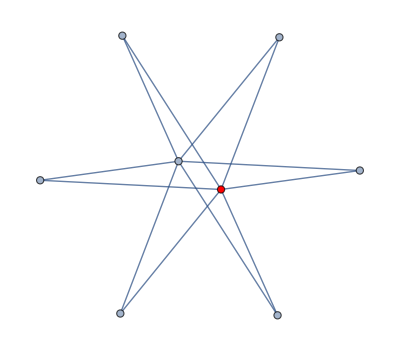

```mathematica
FiniteGroupData["Quaternion","CycleGraph"]
```

```mathematica
FiniteGroupData["Quaternion","ElementNames"]
```

{1,i,j,k,-1,-i,-j,-k}

```mathematica
CycleGraph["Quaternion"]
```

CycleGraph::intpm: Positive machine-sized integer expected at position 1 in CycleGraph[Quaternion].

CycleGraph[Quaternion]

```mathematica
FiniteGroupData["Quaternion","Generators"]
```

{2,3}

```mathematica
FiniteGroupData["Quaternion","InverseGenerators"]
```

{6,7}

```mathematica
FiniteGroupData["Quaternion","MultiplicationTable"]
```

{{1,2,3,4,5,6,7,8},{2,5,4,7,6,1,8,3},{3,8,5,2,7,4,1,6},{4,3,6,5,8,7,2,1},{5,6,7,8,1,2,3,4},{6,1,8,3,2,5,4,7},{7,4,1,6,3,8,5,2},{8,7,2,1,4,3,6,5}}

```mathematica
FiniteGroupData["Quaternion","Center"]
```

{SymmetricGroup,2}

```mathematica
FiniteGroupData["Quaternion","NormalSubgroups"]
```

{Trivial,{CyclicGroup,2},{CyclicGroup,4},Quaternion}

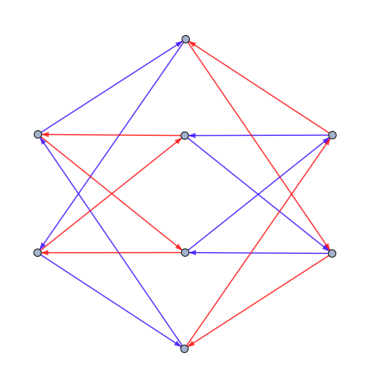

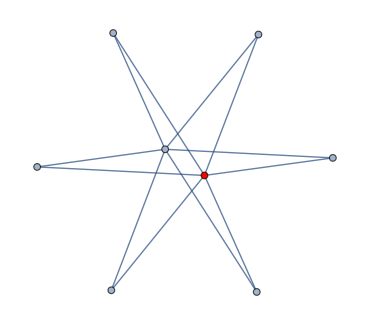

Missing[NotAvailable]

CycleGraph::intpm: Positive machine-sized integer expected at position 1 in CycleGraph[{CyclicGroup, 2}].

CycleGraph[{CyclicGroup,2}]

```mathematica
FiniteGroupData["Quaternion","CayleyGraph"]
FiniteGroupData["Quaternion","CycleGraph"]
FiniteGroupData["Quaternion","DefiningRelations"]
CycleGraph[{"CyclicGroup",2}]
```

```mathematica
FiniteGroupData["Octnion","CayleyGraph"]
FiniteGroupData["Quaternion","CycleGraph"]
FiniteGroupData["Quaternion","DefiningRelations"]
CycleGraph[{"CyclicGroup",2}]
```

FiniteGroupData::notent: Octnion is not a known entity, class, or tag for FiniteGroupData. Use FiniteGroupData[] for a list of entities.

FiniteGroupData[Octnion,CayleyGraph]

-Graphics-

Missing[NotAvailable]

CycleGraph::intpm: Positive machine-sized integer expected at position 1 in CycleGraph[{CyclicGroup, 2}].

CycleGraph[{CyclicGroup,2}]

```mathematica
FiniteGroupData["Octnion","CayleyGraph"]
```

FiniteGroupData::notent: Octnion is not a known entity, class, or tag for FiniteGroupData. Use FiniteGroupData[] for a list of entities.

FiniteGroupData[Octnion,CayleyGraph]

```mathematica
FiniteGroupData["Reflection","CayleyGraph"]
```

-Graphics-

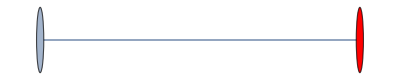

```mathematica
FiniteGroupData["Reflection","CycleGraph"]
```

```mathematica
FiniteGroupData["Quaternion","SpaceRepresentation"]
```

Missing[NotApplicable]

```mathematica
CayleyGraph["Quaternion",VertexLabels->Placed["Name",Center],VertexSize->0.4]
```

CayleyGraph::grp: Quaternion is not a valid group.

CayleyGraph[Quaternion,VertexLabels→Placed[Name,Center],VertexSize→0.4]

```mathematica
--
```

```mathematica
FiniteGroupData["Quaternion","DefiningRelations"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","Inverses"]
```

{1,6,7,8,5,2,3,4}

```mathematica
FiniteGroupData["Quaternion","Order"]
```

8

```mathematica
FiniteGroupData["Quaternion","CommutatorSubgroup"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","ConjugacyClasses"]
```

{{1},{5},{2,6},{3,7},{4,8}}

```mathematica
FiniteGroupData["Quaternion","SylowSubgroups"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","AutomorphismGroup"]
```

{SymmetricGroup,4}

```mathematica
FiniteGroupData["Quaternion","InnerAutomorphismGroup"]
```

Vierergruppe

```mathematica
FiniteGroupData["Quaternion","IsomorphicGroups"]
```

{{8,5},{DicyclicGroup,2}}

```mathematica
FiniteGroupData["Quaternion","OuterAutomorphismGroup"]
```

{SymmetricGroup,3}

```mathematica
FiniteGroupData["Quaternion","SylowSubgroups"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","QuotientGroups"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","SchurCover"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","SchurMultiplier"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","CycleIndex"]
```

1/8 (#1^8+#2^4+6 #4^2)&

```mathematica
FiniteGroupData["Quaternion","Cycles"]
```

{{1},{2,5,6,1},{3,5,7,1},{4,5,8,1},{5,1},{6,5,2,1},{7,5,3,1},{8,5,4,1}}

```mathematica
FiniteGroupData["Quaternion","PermutationRepresentation"]
```

{{1,2,3,4,5,6,7,8},{2,5,4,7,6,1,8,3},{3,8,5,2,7,4,1,6},{4,3,6,5,8,7,2,1},{5,6,7,8,1,2,3,4},{6,1,8,3,2,5,4,7},{7,4,1,6,3,8,5,2},{8,7,2,1,4,3,6,5}}

```mathematica
FiniteGroupData["Quaternion","PermutationGroupRepresentation"]
```

PermutationGroup[{Cycles[{{1,2,5,6},{3,4,7,8}}],Cycles[{{1,3,5,7},{2,8,6,4}}]}]

```mathematica
FiniteGroupData["Quaternion","Transitivity"]
```

Missing[NotAvailable]

```mathematica
FiniteGroupData["Quaternion","CharacterTable"]
```

{{1,1,1,1,1},{1,1,1,-1,-1},{1,1,-1,1,-1},{1,1,-1,-1,1},{2,-2,0,0,0}}

```mathematica
FiniteGroupData["Quaternion","MatrixRepresentation"]
```

{{{1,0},{0,1}},{{-ⅈ,0},{0,ⅈ}},{{0,1},{-1,0}},{{0,-ⅈ},{-ⅈ,0}},{{-1,0},{0,-1}},{{ⅈ,0},{0,-ⅈ}},{{0,-1},{1,0}},{{0,ⅈ},{ⅈ,0}}}

```mathematica
FiniteGroupData["Quaternion","MatrixRepresentation"]//MatrixForm
```

((1
0) | (0
1)
(-ⅈ
0) | (0
ⅈ)
(0
1) | (-1
0)
(0
-ⅈ) | (-ⅈ
0)
(-1
0) | (0
-1)
(ⅈ
0) | (0
-ⅈ)
(0
-1) | (1
0)
(0
ⅈ) | (ⅈ
0))

```mathematica
FiniteGroupData["Quaternion","Orbifold"]
```

Missing[NotApplicable]

```mathematica
FiniteGroupData["Quaternion","AlternateNames"]
```

{}

```mathematica
FiniteGroupData["Quaternion","StandardName"]
```

Quaternion

```mathematica
FiniteGroupData["Quaternion","Information"]
```

http://mathworld.wolfram.com/QuaternionGroup.html

```mathematica
FiniteGroupData["Quaternion","SylowSubgroups"]
```

Missing[NotAvailable]

```mathematica
If
```

If

```mathematica
Matrices[{4,4}]
```

Matrices[{4,4},ℂ,{}]

```mathematica
{{I},{-I}}
```

{{ⅈ},{-ⅈ}}

```mathematica
{{I},{-I}}//MatrixForm
```

(ⅈ
-ⅈ)

```mathematica
{{{I},{-I}},{{I},{-I}},{{I},{-I}},{{I},{-I}}}
```

{{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}}

```mathematica
{{{I},{-I}},{{I},{-I}},{{I},{-I}},{{I},{-I}}}//MatrixForm
```

((ⅈ) | (-ⅈ)
(ⅈ) | (-ⅈ)
(ⅈ) | (-ⅈ)
(ⅈ) | (-ⅈ))

```mathematica
Cell
```

Cell

```mathematica
{{I}.{-I}}
```

{1}

```mathematica
{{I},{-I}}.{{I},{-I}}
```

Dot::dotsh: Tensors {{ⅈ},{-ⅈ}} and {{ⅈ},{-ⅈ}} have incompatible shapes.

{{ⅈ},{-ⅈ}}.{{ⅈ},{-ⅈ}}

```mathematica
Dot[{{ⅈ},{-ⅈ}},{{ⅈ},{-ⅈ}}]
```

Dot::dotsh: Tensors {{ⅈ},{-ⅈ}} and {{ⅈ},{-ⅈ}} have incompatible shapes.

{{ⅈ},{-ⅈ}}.{{ⅈ},{-ⅈ}}

```mathematica
I   I   I   I   I   I   I   I   I   I   I   I   I
```

ⅈ

```mathematica
{I[1],I[2],I[3],I[4]}
```

{ⅈ[1],ⅈ[2],ⅈ[3],ⅈ[4]}

```mathematica
gI[1]=I
gI[2]=I
gI[3]=I
gI[4]=I
```

ⅈ

ⅈ

ⅈ

«1 more identical outputs»

```mathematica
gI[1].gI[4]
```

ⅈ.ⅈ

```mathematica
ⅈ.ⅈ
```

ⅈ.ⅈ

```mathematica
I.I
```

ⅈ.ⅈ

```mathematica
gestult[1]=I
gestult[2]=-I
p=1
```

ⅈ

-ⅈ

1

```mathematica
Grid[gestult[p],{6,6}]
```

Grid[ⅈ,{6,6}]

```mathematica
Grid[ⅈ,{1,2}]
```

Grid[ⅈ,{1,2}]

```mathematica
Grid[Table[gestult[p],{6},{6}],Frame->All]
```

ⅈ | ⅈ | ⅈ | ⅈ | ⅈ | ⅈ
ⅈ | ⅈ | ⅈ | ⅈ | ⅈ | ⅈ
ⅈ | ⅈ | ⅈ | ⅈ | ⅈ | ⅈ
ⅈ | ⅈ | ⅈ | ⅈ | ⅈ | ⅈ
ⅈ | ⅈ | ⅈ | ⅈ | ⅈ | ⅈ
ⅈ | ⅈ | ⅈ | ⅈ | ⅈ | ⅈ

```mathematica
theGestult=Grid[gestult[1],,Conjugate[gestult[1]],Frame->All]
```

Grid[ⅈ,Null,-ⅈ,Frame→All]

```mathematica
theGestult
```

Grid[ⅈ,Null,-ⅈ,Frame→All]

```mathematica
theGestult=Grid[Table[{gestult[1],,Conjugate[gestult[1]]},{1},{1}],Frame->All]
```

{ⅈ,Null,-ⅈ}

```mathematica
Grid[{{gestult[1]},{},{Conjugate[gestult[1]]}},Frame->All]
```

ⅈ

-ⅈ

```mathematica
Grid[{{gestult[1]},{Conjugate[gestult[1]]}},Frame->All]
```

ⅈ
-ⅈ

```mathematica
theNull=Null//N
```

```mathematica
Grid[{{theNull},{gestult[1],Null,Conjugate[gestult[1]]}},Frame->All]
```

|  | 
ⅈ |  | -ⅈ

```mathematica
Grid[{{gestult[1],,Conjugate[gestult[1]]}},Frame->All]
```

ⅈ |  | -ⅈ

```mathematica
0!
```

1

```mathematica
Grid
```

Grid

```mathematica
Grid[Table[Null,{17},{17}],Frame->All]
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
{{□, □, □, □, □, □, □, □, □, zeroD Octhoginal

 Existance[Unity]
 Reflection Null;Null Reflection Existance[Unity]

oneD Octhoginal reflection

3. Additive identity:There exists an element 0 in S such that for all a in S,0+a=a+0=a, NULLPLAIN
Sum===1===Null, Reflection, □, □, □, □, □, □, □, □}, {0, , □, □, +, , , gestultPhaseCntNp1[0], , 4. Additive inverse:For every a in S there exists-a in S such that a+(-a)=(-a)+a=0, {Null,{+,-}}, , , , , , , , □, }, {1, 1, □, cmplxOne[1], I, , , gestultPhaseCntNp1[1], □, +, {+,-}
Conjugate
+^2=I;-^2=I, -, , , , , , , □, }, {2, 2, realOne[1], cmplxTwo[2], 2I, 1, , gestultPhaseCntNp1[2], □, +I, {+I,1}
+I^2=1;-I^2=1, -I, □, , , , , , □, }, {3, 4, realTwo[2], cmplxFour[4], 4I, 2, □, gestultPhaseCntNp1[4], □, □, □, □, , -gestultPhaseCntNp1[4], -I, -J, -K, , □, }, {4, 8, realFour[4], cmplxEight[8], , , , , , , , , , , , , , , □, }, {5, 16, realEight[8], cmplxSinteen[16], , , , , , , , , , , , , , , □, }, {6, , realSinteen[16], □, , , , , , , , , , , , , , , □, }, {7, , □, □, , , , , , , , , , , , , , , □, }, {8, , □, □, , , , , , , , , , , , , , , □, }, {9, , □, □, , , , , , , , , , , , , , , □, }, {, , □, □, , , , , , , , , , , , , , , □, }, {, , □, □, , , , , , , , , , , , , , , □, }, {, , □, □, , , , , , , , , , , , , , , □, }, {, , □, □, , , , , , , , , , , , , , , □, }, {, , □, □, , , , , , , , , , , , , , , □, }, {, , □, □, , , , , , , , , , , , , , , □, }, {, , □, □, , , , , , , , , , , , , , , □, }}
```

```mathematica
{{□, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }}
{{□, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }}
```

□ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

□ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
{{, , , , , , , , □, , , , , , , , }, {, , , , , , , +1, SpanFromAbove, -1, , , , , , , }, {, , , , , , I, +I, SpanFromAbove, -I, I, , , , , , }, {, , , , , J, , , SpanFromAbove, , , J, , , , , }, {, , , , K, , , , SpanFromAbove, , , , K, , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }}
```

|  |  |  |  |  |  |  | □ |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 1 |  | -1 |  |  |  |  |  |  | 
 |  |  |  |  |  | ⅈ | ⅈ |  | -ⅈ | ⅈ |  |  |  |  |  | 
 |  |  |  |  | J |  |  |  |  |  | J |  |  |  |  | 
 |  |  |  | K |  |  |  |  |  |  |  | K |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
{{, , , , , , , , Null, , , , , , , , }, {, , , , , , , , SpanFromAbove, , , , , , , , }, {, , , , , , , SpanFromAbove, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }, {, , , , , , , □, □, □, , , , , , , }}
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  | 
 |  |  |  |  |  |  | □ | □ | □ |  |  |  |  |  |  |

```mathematica
{{, , , , , , , 6, , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }}
```

|  |  |  |  |  |  | 6 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
{{, , , , , , , , 5, , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , }}
```

|  |  |  |  |  |  |  | 5 |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
5K/2//N
```

2.5 K

```mathematica
{{□, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, -I, -I, -I, -I, -I, , , , , , , , , , , }, {0NL, 0NL, 0NL, 0NL, 0NL, 0NL, , , , , , , , , , , }}
{{□, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }}
{{□, , , , , , , , , , , , , , , , }}
{{1UY, 1UY, 1UY, 1UY, 1UY, 1UY, , , , , , , , , , , }, {, +I, +I, +I, +I, +I, , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }, {, , , , , , , , , , , , , , , , }}
```

□ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | -ⅈ | -ⅈ | -ⅈ | -ⅈ | -ⅈ |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |

{{□,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

{{□,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

UY | UY | UY | UY | UY | UY |  |  |  |  |  |  |  |  |  |  | 
 | ⅈ | ⅈ | ⅈ | ⅈ | ⅈ |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
0^2
```

0

```mathematica
1^2
```

1

```mathematica
(Sqrt[(0)^2+ (1)^2])
```

1

```mathematica
((-I)+ (+I))
```

0

```mathematica
(Sqrt[(-I)^2+ (+I)^2])
```

ⅈ √2

```mathematica
(-I)^2
```

-1

```mathematica
(+I)^2
```

-1

```mathematica
---
```

```mathematica
Clear[x1,x2,x2,epsolonP,epsolonH]
```

```mathematica
x1^2+x2^2+x3^2==0
```

x1^2+x2^2==0

```mathematica
x1 ==epsolonP^2 - epsolonH^2
x2 ==I(epsolonP^2 + epsolonH^2)
```

x1==-epsolonH^2+epsolonP^2

x2==ⅈ (epsolonH^2+epsolonP^2)

```mathematica
x3 == -2  epsolonP^2 epsolonH^2
```

0==-2 epsolonH^2 epsolonP^2

```mathematica
Clear[x1,x2,x3,epsolonP,epsolonH]
```

```mathematica
-1^(1/2)
```

-1

```mathematica
epsolonN=1
epsolonU=0
```

1

0

```mathematica
x1^2+x2^2+x3^2==0

x1 ==epsolonN^2 - epsolonU^2
x2 ==I(epsolonN^2 + epsolonU^2)

x3 == -2  epsolonN^2 epsolonU^2
```

x1^2+x2^2+x3^2==0

x1==1

x2==ⅈ

x3==0

```mathematica
Solve[{x1^2+x2^2+x3^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2}]
```

{{x1→1,x2→-ⅈ,x3→0}}

```mathematica
Solve[{x1^2 ==0,x1 == ζ0^2 - ζ1^2(*,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2*)}]
```

{}

```mathematica
ζ0==0
ζ1==1
```

True

False

```mathematica
ζ0==0
ζ1==1
Solve[{x1^2 ==0,x1 == ζ0^2 - ζ1^2(*,x2 == I(ζ0^2 + ζ1^2),x3 == -2ζ0^2ζ1^2*)}]
```

True

False

{}

```mathematica
ζ0==0
ζ1==1
Solve[{x1^2 ==0,x1 == ζ0^2 - ζ1^2,x2 == I(ζ0^2 + ζ1^2)(*,x3 == -2ζ0^2ζ1^2*)}]
```

True

False

{}